```mathematica
ClearAll["Global`*"]
```

```mathematica
tk[n_,k_, a_]:= Sum[ tk[n/j,k-1,a],{j,2,n}]-a Sum[ tk[n/(a j),k-1,a],{j,1,n/a}];tk[n_,0,a_]:=1

tki[n_,k_,k2_,a_]:=tki[n,k,k2,a]=Sum[ tki[n/j,k-1,k2,a],{j,2,n}]
tki[n_,0,k2_,a_]:=tkp[n,k2,a]
tkp[n_,k_,a_]:=tkp[n,k,a]=Sum[ tkp[n/(a j),k-1,a],{j,1,n/a}]
tkp[n_,0,a_]:=1
tk2[n_,k_,a_]:=tk2[n,k,a]=Sum[ (-1)^j a^j Binomial[k,j]tki[n,k-j,j,a],{j,0,k}]
tk2s[n_,k_,j_,a_]:=(-1)^j a^j Binomial[k,j]tki[n,k-j,j,a]
tk2s2[n_,k_,j_,a_]:=tki[n,k-j,j,a]

D1[n_,k_]:=Sum[D1[Floor[n/j],k-1],{j,1,n}];D1[n_,0]:=1
Lina[n_,a_]:=Sum[ ((-1)^(k+1) tk2[n,k,a]+1)/k + (a^k-1)/k,{k,1,Log[a,n]}]
Linb[n_,a_]:=Sum[ (-1)^(k+1)/k tk[n,k,a],{k,1,Log[2,n]}]+Sum[ a^k/k,{k,1,Log[a,n]}]
Lin2[n_,a_]:=If[a>=2,Linb[n,a],Lina[n,a]]

st[n_,a_,k_]:=If[tk2[a,n,k]≠0,(-1)^(n+1)/n tk2[a,n,k] + 1/n,0]
```

```mathematica
Lina[100,1.03]
```

28.5333

```mathematica
tk[1000,4,1.2]
```

-1357.35

```mathematica
tk2[1000,4,1.2]
```

-1357.35

```mathematica
Table[{n,(-1)^(n+1)/n tk[8,n,1.1]},{n,1,25}]//TableForm
{{1, -0.7000000000000011}, {2, -1.0700000000000003}, {3, -0.748333333333334}, {4, 4.770425000000001}, {5, -4.647852000000002}, {6, -0.8150156666666672}, {7, -0.8581717571428582}, {8, 8.731581278750005}, {9, -8.485580349888895}, {10, -0.730963784210001}, {11, 2.074993968080002}, {12, -0.5468473686710844}, {13, -0.5794021618561859}, {14, -0.6164770025701977}, {15, 3.519015124538037}, {16, -0.28718581164732637}, {17, -0.2973217814701732}, {18, -0.3088842951940132}, {19, -0.32188994972849805}, {20, -0.3363749974662805}, {21, -0.35239285448848434}, {22, 0.}, {23, 0.}, {24, 0.}, {25, 0.}}
```

```mathematica
Table[{n,1.04^n,(-1)^(n+1)/n tk[8,n,1.04]},{n,1,54}]//TableForm
```

1 | 1.04 | -0.28
2 | 1.0816 | -1.7928
3 | 1.12486 | -0.306197
4 | 1.16986 | 0.599639
5 | 1.21665 | -0.488101
6 | 1.26532 | -0.468255
7 | 1.31593 | -0.458574
8 | 1.36857 | 10.493
9 | 1.42331 | -10.913
10 | 1.48024 | -0.385608
11 | 1.53945 | -0.388176
12 | 1.60103 | 1.20827
13 | 1.66507 | -0.334985
14 | 1.73168 | -0.340151
15 | 1.80094 | -0.346513
16 | 1.87298 | -0.353955
17 | 1.9479 | -0.362392
18 | 2.02582 | 18.8735
19 | 2.10685 | -17.8041
20 | 2.19112 | -0.278104
21 | 2.27877 | -0.283803
22 | 2.36992 | -0.290025
23 | 2.46472 | -0.296755
24 | 2.5633 | -0.303982
25 | 2.66584 | -0.311698
26 | 2.77247 | 2.45257
27 | 2.88337 | -0.21769
28 | 2.9987 | -0.222431
29 | 3.11865 | -0.227488
30 | 3.2434 | -0.232859
31 | 3.37313 | -0.238547
32 | 3.50806 | -0.244552
33 | 3.64838 | -0.250879
34 | 3.79432 | -0.257533
35 | 3.94609 | -0.264518
36 | 4.10393 | 3.83209
37 | 4.26809 | -0.115354
38 | 4.43881 | -0.116811
39 | 4.61637 | -0.118368
40 | 4.80102 | -0.120026
41 | 4.99306 | -0.121782
42 | 5.19278 | -0.123638
43 | 5.4005 | -0.125593
44 | 5.61652 | -0.127648
45 | 5.84118 | -0.129804
46 | 6.07482 | -0.132061
47 | 6.31782 | -0.134422
48 | 6.57053 | -0.136886
49 | 6.83335 | -0.139456
50 | 7.10668 | -0.142134
51 | 7.39095 | -0.144921
52 | 7.68659 | -0.147819
53 | 7.99405 | -0.150831
54 | 8.31381 | 0.

```mathematica
Table[{n,1.01^n,(-1)^(n+1)/n tk2[8,n,1.01]},{n,1,210}]//TableForm
```

1 | 1.01 | -0.07
2 | 1.0201 | -1.5708
3 | 1.0303 | -0.0716093
4 | 1.0406 | -0.322428
5 | 1.05101 | -0.273256
6 | 1.06152 | -0.240761
7 | 1.07214 | -0.217799
8 | 1.08286 | -0.2008
9 | 1.09369 | -0.187779
10 | 1.10462 | -0.177545
11 | 1.11567 | -0.169342
12 | 1.12683 | -0.162665
13 | 1.13809 | -0.157163
14 | 1.14947 | 0.996886
15 | 1.16097 | -0.137262
16 | 1.17258 | -0.133921
17 | 1.1843 | -0.13108
18 | 1.19615 | -0.128658
19 | 1.20811 | -0.12659
20 | 1.22019 | -0.124824
21 | 1.23239 | -0.123319
22 | 1.24472 | -0.122041
23 | 1.25716 | -0.120962
24 | 1.26973 | -0.120058
25 | 1.28243 | -0.11931
26 | 1.29526 | -0.118701
27 | 1.30821 | -0.118216
28 | 1.32129 | -0.117845
29 | 1.3345 | 38.583
30 | 1.34785 | -38.4177
31 | 1.36133 | -0.0998295
32 | 1.37494 | -0.0995092
33 | 1.38869 | -0.0992573
34 | 1.40258 | -0.0990685
35 | 1.4166 | -0.0989382
36 | 1.43077 | -0.0988622
37 | 1.44508 | -0.0988368
38 | 1.45953 | -0.0988586
39 | 1.47412 | -0.0989247
40 | 1.48886 | -0.0990326
41 | 1.50375 | -0.0991797
42 | 1.51879 | -0.0993639
43 | 1.53398 | -0.0995834
44 | 1.54932 | -0.0998363
45 | 1.56481 | -0.100121
46 | 1.58046 | -0.100436
47 | 1.59626 | -0.10078
48 | 1.61223 | 1.51107
49 | 1.62835 | -0.0854294
50 | 1.64463 | -0.085693
51 | 1.66108 | -0.08598
52 | 1.67769 | -0.0862894
53 | 1.69447 | -0.0866205
54 | 1.71141 | -0.0869726
55 | 1.72852 | -0.0873451
56 | 1.74581 | -0.0877373
57 | 1.76327 | -0.0881487
58 | 1.7809 | -0.0885788
59 | 1.79871 | -0.0890271
60 | 1.8167 | -0.0894932
61 | 1.83486 | -0.0899768
62 | 1.85321 | -0.0904774
63 | 1.87174 | -0.0909947
64 | 1.89046 | -0.0915284
65 | 1.90937 | -0.0920783
66 | 1.92846 | -0.0926441
67 | 1.94774 | -0.0932255
68 | 1.96722 | -0.0938224
69 | 1.98689 | -0.0944346
70 | 2.00676 | 71.145
71 | 2.02683 | -69.61
72 | 2.0471 | -0.0689686
73 | 2.06757 | -0.0692649
74 | 2.08825 | -0.0695709
75 | 2.10913 | -0.0698866
76 | 2.13022 | -0.0702118
77 | 2.15152 | -0.0705462
78 | 2.17304 | -0.0708899
79 | 2.19477 | -0.0712426
80 | 2.21672 | -0.0716043
81 | 2.23888 | -0.0719748
82 | 2.26127 | -0.0723541
83 | 2.28388 | -0.0727421
84 | 2.30672 | -0.0731387
85 | 2.32979 | -0.0735437
86 | 2.35309 | -0.0739573
87 | 2.37662 | -0.0743792
88 | 2.40038 | -0.0748095
89 | 2.42439 | -0.075248
90 | 2.44863 | -0.0756948
91 | 2.47312 | -0.0761498
92 | 2.49785 | -0.0766129
93 | 2.52283 | -0.0770842
94 | 2.54806 | -0.0775636
95 | 2.57354 | -0.078051
96 | 2.59927 | -0.0785465
97 | 2.62527 | -0.0790501
98 | 2.65152 | -0.0795616
99 | 2.67803 | 2.59795
100 | 2.70481 | -0.0538285
101 | 2.73186 | -0.0540963
102 | 2.75918 | -0.0543694
103 | 2.78677 | -0.0546478
104 | 2.81464 | -0.0549316
105 | 2.84279 | -0.0552206
106 | 2.87121 | -0.0555148
107 | 2.89993 | -0.0558143
108 | 2.92893 | -0.0561189
109 | 2.95822 | -0.0564288
110 | 2.9878 | -0.0567439
111 | 3.01768 | -0.0570642
112 | 3.04785 | -0.0573897
113 | 3.07833 | -0.0577204
114 | 3.10911 | -0.0580562
115 | 3.1402 | -0.0583973
116 | 3.17161 | -0.0587435
117 | 3.20332 | -0.0590949
118 | 3.23536 | -0.0594515
119 | 3.26771 | -0.0598133
120 | 3.30039 | -0.0601803
121 | 3.33339 | -0.0605526
122 | 3.36672 | -0.06093
123 | 3.40039 | -0.0613127
124 | 3.4344 | -0.0617007
125 | 3.46874 | -0.0620939
126 | 3.50343 | -0.0624924
127 | 3.53846 | -0.0628962
128 | 3.57385 | -0.0633053
129 | 3.60958 | -0.0637197
130 | 3.64568 | -0.0641395
131 | 3.68214 | -0.0645647
132 | 3.71896 | -0.0649953
133 | 3.75615 | -0.0654313
134 | 3.79371 | -0.0658727
135 | 3.83165 | -0.0663197
136 | 3.86996 | -0.0667721
137 | 3.90866 | -0.06723
138 | 3.94775 | -0.0676935
139 | 3.98723 | -0.0681626
140 | 4.0271 | 3.95846
141 | 4.06737 | -0.0288466
142 | 4.10804 | -0.0289299
143 | 4.14912 | -0.0290149
144 | 4.19062 | -0.0291015
145 | 4.23252 | -0.0291898
146 | 4.27485 | -0.0292798
147 | 4.3176 | -0.0293714
148 | 4.36077 | -0.0294647
149 | 4.40438 | -0.0295596
150 | 4.44842 | -0.0296562
151 | 4.49291 | -0.0297544
152 | 4.53784 | -0.0298542
153 | 4.58321 | -0.0299557
154 | 4.62905 | -0.0300587
155 | 4.67534 | -0.0301635
156 | 4.72209 | -0.0302698
157 | 4.76931 | -0.0303778
158 | 4.817 | -0.0304874
159 | 4.86517 | -0.0305986
160 | 4.91383 | -0.0307114
161 | 4.96296 | -0.0308259
162 | 5.01259 | -0.0309419
163 | 5.06272 | -0.0310596
164 | 5.11335 | -0.0311789
165 | 5.16448 | -0.0312999
166 | 5.21613 | -0.0314224
167 | 5.26829 | -0.0315466
168 | 5.32097 | -0.0316724
169 | 5.37418 | -0.0317999
170 | 5.42792 | -0.0319289
171 | 5.4822 | -0.0320597
172 | 5.53702 | -0.032192
173 | 5.59239 | -0.032326
174 | 5.64832 | -0.0324616
175 | 5.7048 | -0.0325989
176 | 5.76185 | -0.0327378
177 | 5.81947 | -0.0328783
178 | 5.87766 | -0.0330206
179 | 5.93644 | -0.0331645
180 | 5.9958 | -0.03331
181 | 6.05576 | -0.0334572
182 | 6.11632 | -0.0336061
183 | 6.17748 | -0.0337567
184 | 6.23926 | -0.033909
185 | 6.30165 | -0.034063
186 | 6.36466 | -0.0342186
187 | 6.42831 | -0.034376
188 | 6.49259 | -0.0345351
189 | 6.55752 | -0.0346959
190 | 6.6231 | -0.0348584
191 | 6.68933 | -0.0350227
192 | 6.75622 | -0.0351886
193 | 6.82378 | -0.0353564
194 | 6.89202 | -0.0355259
195 | 6.96094 | -0.0356971
196 | 7.03055 | -0.0358701
197 | 7.10085 | -0.0360449
198 | 7.17186 | -0.0362215
199 | 7.24358 | -0.0363999
200 | 7.31602 | -0.0365801
201 | 7.38918 | -0.0367621
202 | 7.46307 | -0.0369459
203 | 7.5377 | -0.0371315
204 | 7.61308 | -0.037319
205 | 7.68921 | -0.0375083
206 | 7.7661 | -0.0376995
207 | 7.84376 | -0.0378926
208 | 7.9222 | -0.0380875
209 | 8.00142 | 0.
210 | 8.08144 | 0.

```mathematica
Table[{n,1.01^n,(-1)^(n+1)/n tk2[8,n,1.01],
tk2s2[8,n,n-3,1.01],
tk2s2[8,n,n-2,1.01],
tk2s2[8,n,n-1,1.01],
tk2s2[8,n,n,1.01]},{n,1,210}]//TableForm
```

1 | 1.01 | -0.07 | 0 | 0 | 7 | 7
2 | 1.0201 | -1.5708 | 0 | 5 | 9 | 16
3 | 1.0303 | -0.0716093 | 1 | 3 | 12 | 28
4 | 1.0406 | -0.322428 | 0 | 3 | 15 | 43
5 | 1.05101 | -0.273256 | 0 | 3 | 18 | 61
6 | 1.06152 | -0.240761 | 0 | 3 | 21 | 82
7 | 1.07214 | -0.217799 | 0 | 3 | 24 | 106
8 | 1.08286 | -0.2008 | 0 | 3 | 27 | 133
9 | 1.09369 | -0.187779 | 0 | 3 | 30 | 163
10 | 1.10462 | -0.177545 | 0 | 3 | 33 | 196
11 | 1.11567 | -0.169342 | 0 | 3 | 36 | 232
12 | 1.12683 | -0.162665 | 0 | 3 | 39 | 271
13 | 1.13809 | -0.157163 | 0 | 3 | 42 | 313
14 | 1.14947 | 0.996886 | 0 | 3 | 45 | 344
15 | 1.16097 | -0.137262 | 0 | 3 | 47 | 391
16 | 1.17258 | -0.133921 | 0 | 3 | 50 | 441
17 | 1.1843 | -0.13108 | 0 | 3 | 53 | 494
18 | 1.19615 | -0.128658 | 0 | 3 | 56 | 550
19 | 1.20811 | -0.12659 | 0 | 3 | 59 | 609
20 | 1.22019 | -0.124824 | 0 | 3 | 62 | 671
21 | 1.23239 | -0.123319 | 0 | 3 | 65 | 736
22 | 1.24472 | -0.122041 | 0 | 3 | 68 | 804
23 | 1.25716 | -0.120962 | 0 | 3 | 71 | 875
24 | 1.26973 | -0.120058 | 0 | 3 | 74 | 949
25 | 1.28243 | -0.11931 | 0 | 3 | 77 | 1026
26 | 1.29526 | -0.118701 | 0 | 3 | 80 | 1106
27 | 1.30821 | -0.118216 | 0 | 3 | 83 | 1189
28 | 1.32129 | -0.117845 | 0 | 3 | 86 | 1275
29 | 1.3345 | 38.583 | 0 | 3 | 89 | 523
30 | 1.34785 | -38.4177 | 0 | 3 | 33 | 556
31 | 1.36133 | -0.0998295 | 0 | 1 | 34 | 590
32 | 1.37494 | -0.0995092 | 0 | 1 | 35 | 625
33 | 1.38869 | -0.0992573 | 0 | 1 | 36 | 661
34 | 1.40258 | -0.0990685 | 0 | 1 | 37 | 698
35 | 1.4166 | -0.0989382 | 0 | 1 | 38 | 736
36 | 1.43077 | -0.0988622 | 0 | 1 | 39 | 775
37 | 1.44508 | -0.0988368 | 0 | 1 | 40 | 815
38 | 1.45953 | -0.0988586 | 0 | 1 | 41 | 856
39 | 1.47412 | -0.0989247 | 0 | 1 | 42 | 898
40 | 1.48886 | -0.0990326 | 0 | 1 | 43 | 941
41 | 1.50375 | -0.0991797 | 0 | 1 | 44 | 985
42 | 1.51879 | -0.0993639 | 0 | 1 | 45 | 1030
43 | 1.53398 | -0.0995834 | 0 | 1 | 46 | 1076
44 | 1.54932 | -0.0998363 | 0 | 1 | 47 | 1123
45 | 1.56481 | -0.100121 | 0 | 1 | 48 | 1171
46 | 1.58046 | -0.100436 | 0 | 1 | 49 | 1220
47 | 1.59626 | -0.10078 | 0 | 1 | 50 | 1270
48 | 1.61223 | 1.51107 | 0 | 1 | 51 | 1273
49 | 1.62835 | -0.0854294 | 0 | 1 | 51 | 1324
50 | 1.64463 | -0.085693 | 0 | 1 | 52 | 1376
51 | 1.66108 | -0.08598 | 0 | 1 | 53 | 1429
52 | 1.67769 | -0.0862894 | 0 | 1 | 54 | 1483
53 | 1.69447 | -0.0866205 | 0 | 1 | 55 | 1538
54 | 1.71141 | -0.0869726 | 0 | 1 | 56 | 1594
55 | 1.72852 | -0.0873451 | 0 | 1 | 57 | 1651
56 | 1.74581 | -0.0877373 | 0 | 1 | 58 | 1709
57 | 1.76327 | -0.0881487 | 0 | 1 | 59 | 1768
58 | 1.7809 | -0.0885788 | 0 | 1 | 60 | 1828
59 | 1.79871 | -0.0890271 | 0 | 1 | 61 | 1889
60 | 1.8167 | -0.0894932 | 0 | 1 | 62 | 1951
61 | 1.83486 | -0.0899768 | 0 | 1 | 63 | 2014
62 | 1.85321 | -0.0904774 | 0 | 1 | 64 | 2078
63 | 1.87174 | -0.0909947 | 0 | 1 | 65 | 2143
64 | 1.89046 | -0.0915284 | 0 | 1 | 66 | 2209
65 | 1.90937 | -0.0920783 | 0 | 1 | 67 | 2276
66 | 1.92846 | -0.0926441 | 0 | 1 | 68 | 2344
67 | 1.94774 | -0.0932255 | 0 | 1 | 69 | 2413
68 | 1.96722 | -0.0938224 | 0 | 1 | 70 | 2483
69 | 1.98689 | -0.0944346 | 0 | 1 | 71 | 2554
70 | 2.00676 | 71.145 | 0 | 1 | 72 | 141
71 | 2.02683 | -69.61 | 0 | 1 | 2 | 143
72 | 2.0471 | -0.0689686 | 0 | 0 | 2 | 145
73 | 2.06757 | -0.0692649 | 0 | 0 | 2 | 147
74 | 2.08825 | -0.0695709 | 0 | 0 | 2 | 149
75 | 2.10913 | -0.0698866 | 0 | 0 | 2 | 151
76 | 2.13022 | -0.0702118 | 0 | 0 | 2 | 153
77 | 2.15152 | -0.0705462 | 0 | 0 | 2 | 155
78 | 2.17304 | -0.0708899 | 0 | 0 | 2 | 157
79 | 2.19477 | -0.0712426 | 0 | 0 | 2 | 159
80 | 2.21672 | -0.0716043 | 0 | 0 | 2 | 161
81 | 2.23888 | -0.0719748 | 0 | 0 | 2 | 163
82 | 2.26127 | -0.0723541 | 0 | 0 | 2 | 165
83 | 2.28388 | -0.0727421 | 0 | 0 | 2 | 167
84 | 2.30672 | -0.0731387 | 0 | 0 | 2 | 169
85 | 2.32979 | -0.0735437 | 0 | 0 | 2 | 171
86 | 2.35309 | -0.0739573 | 0 | 0 | 2 | 173
87 | 2.37662 | -0.0743792 | 0 | 0 | 2 | 175
88 | 2.40038 | -0.0748095 | 0 | 0 | 2 | 177
89 | 2.42439 | -0.075248 | 0 | 0 | 2 | 179
90 | 2.44863 | -0.0756948 | 0 | 0 | 2 | 181
91 | 2.47312 | -0.0761498 | 0 | 0 | 2 | 183
92 | 2.49785 | -0.0766129 | 0 | 0 | 2 | 185
93 | 2.52283 | -0.0770842 | 0 | 0 | 2 | 187
94 | 2.54806 | -0.0775636 | 0 | 0 | 2 | 189
95 | 2.57354 | -0.078051 | 0 | 0 | 2 | 191
96 | 2.59927 | -0.0785465 | 0 | 0 | 2 | 193
97 | 2.62527 | -0.0790501 | 0 | 0 | 2 | 195
98 | 2.65152 | -0.0795616 | 0 | 0 | 2 | 197
99 | 2.67803 | 2.59795 | 0 | 0 | 2 | 100
100 | 2.70481 | -0.0538285 | 0 | 0 | 1 | 101
101 | 2.73186 | -0.0540963 | 0 | 0 | 1 | 102
102 | 2.75918 | -0.0543694 | 0 | 0 | 1 | 103
103 | 2.78677 | -0.0546478 | 0 | 0 | 1 | 104
104 | 2.81464 | -0.0549316 | 0 | 0 | 1 | 105
105 | 2.84279 | -0.0552206 | 0 | 0 | 1 | 106
106 | 2.87121 | -0.0555148 | 0 | 0 | 1 | 107
107 | 2.89993 | -0.0558143 | 0 | 0 | 1 | 108
108 | 2.92893 | -0.0561189 | 0 | 0 | 1 | 109
109 | 2.95822 | -0.0564288 | 0 | 0 | 1 | 110
110 | 2.9878 | -0.0567439 | 0 | 0 | 1 | 111
111 | 3.01768 | -0.0570642 | 0 | 0 | 1 | 112
112 | 3.04785 | -0.0573897 | 0 | 0 | 1 | 113
113 | 3.07833 | -0.0577204 | 0 | 0 | 1 | 114
114 | 3.10911 | -0.0580562 | 0 | 0 | 1 | 115
115 | 3.1402 | -0.0583973 | 0 | 0 | 1 | 116
116 | 3.17161 | -0.0587435 | 0 | 0 | 1 | 117
117 | 3.20332 | -0.0590949 | 0 | 0 | 1 | 118
118 | 3.23536 | -0.0594515 | 0 | 0 | 1 | 119
119 | 3.26771 | -0.0598133 | 0 | 0 | 1 | 120
120 | 3.30039 | -0.0601803 | 0 | 0 | 1 | 121
121 | 3.33339 | -0.0605526 | 0 | 0 | 1 | 122
122 | 3.36672 | -0.06093 | 0 | 0 | 1 | 123
123 | 3.40039 | -0.0613127 | 0 | 0 | 1 | 124
124 | 3.4344 | -0.0617007 | 0 | 0 | 1 | 125
125 | 3.46874 | -0.0620939 | 0 | 0 | 1 | 126
126 | 3.50343 | -0.0624924 | 0 | 0 | 1 | 127
127 | 3.53846 | -0.0628962 | 0 | 0 | 1 | 128
128 | 3.57385 | -0.0633053 | 0 | 0 | 1 | 129
129 | 3.60958 | -0.0637197 | 0 | 0 | 1 | 130
130 | 3.64568 | -0.0641395 | 0 | 0 | 1 | 131
131 | 3.68214 | -0.0645647 | 0 | 0 | 1 | 132
132 | 3.71896 | -0.0649953 | 0 | 0 | 1 | 133
133 | 3.75615 | -0.0654313 | 0 | 0 | 1 | 134
134 | 3.79371 | -0.0658727 | 0 | 0 | 1 | 135
135 | 3.83165 | -0.0663197 | 0 | 0 | 1 | 136
136 | 3.86996 | -0.0667721 | 0 | 0 | 1 | 137
137 | 3.90866 | -0.06723 | 0 | 0 | 1 | 138
138 | 3.94775 | -0.0676935 | 0 | 0 | 1 | 139
139 | 3.98723 | -0.0681626 | 0 | 0 | 1 | 140
140 | 4.0271 | 3.95846 | 0 | 0 | 1 | 1
141 | 4.06737 | -0.0288466 | 0 | 0 | 0 | 1
142 | 4.10804 | -0.0289299 | 0 | 0 | 0 | 1
143 | 4.14912 | -0.0290149 | 0 | 0 | 0 | 1
144 | 4.19062 | -0.0291015 | 0 | 0 | 0 | 1
145 | 4.23252 | -0.0291898 | 0 | 0 | 0 | 1
146 | 4.27485 | -0.0292798 | 0 | 0 | 0 | 1
147 | 4.3176 | -0.0293714 | 0 | 0 | 0 | 1
148 | 4.36077 | -0.0294647 | 0 | 0 | 0 | 1
149 | 4.40438 | -0.0295596 | 0 | 0 | 0 | 1
150 | 4.44842 | -0.0296562 | 0 | 0 | 0 | 1
151 | 4.49291 | -0.0297544 | 0 | 0 | 0 | 1
152 | 4.53784 | -0.0298542 | 0 | 0 | 0 | 1
153 | 4.58321 | -0.0299557 | 0 | 0 | 0 | 1
154 | 4.62905 | -0.0300587 | 0 | 0 | 0 | 1
155 | 4.67534 | -0.0301635 | 0 | 0 | 0 | 1
156 | 4.72209 | -0.0302698 | 0 | 0 | 0 | 1
157 | 4.76931 | -0.0303778 | 0 | 0 | 0 | 1
158 | 4.817 | -0.0304874 | 0 | 0 | 0 | 1
159 | 4.86517 | -0.0305986 | 0 | 0 | 0 | 1
160 | 4.91383 | -0.0307114 | 0 | 0 | 0 | 1
161 | 4.96296 | -0.0308259 | 0 | 0 | 0 | 1
162 | 5.01259 | -0.0309419 | 0 | 0 | 0 | 1
163 | 5.06272 | -0.0310596 | 0 | 0 | 0 | 1
164 | 5.11335 | -0.0311789 | 0 | 0 | 0 | 1
165 | 5.16448 | -0.0312999 | 0 | 0 | 0 | 1
166 | 5.21613 | -0.0314224 | 0 | 0 | 0 | 1
167 | 5.26829 | -0.0315466 | 0 | 0 | 0 | 1
168 | 5.32097 | -0.0316724 | 0 | 0 | 0 | 1
169 | 5.37418 | -0.0317999 | 0 | 0 | 0 | 1
170 | 5.42792 | -0.0319289 | 0 | 0 | 0 | 1
171 | 5.4822 | -0.0320597 | 0 | 0 | 0 | 1
172 | 5.53702 | -0.032192 | 0 | 0 | 0 | 1
173 | 5.59239 | -0.032326 | 0 | 0 | 0 | 1
174 | 5.64832 | -0.0324616 | 0 | 0 | 0 | 1
175 | 5.7048 | -0.0325989 | 0 | 0 | 0 | 1
176 | 5.76185 | -0.0327378 | 0 | 0 | 0 | 1
177 | 5.81947 | -0.0328783 | 0 | 0 | 0 | 1
178 | 5.87766 | -0.0330206 | 0 | 0 | 0 | 1
179 | 5.93644 | -0.0331645 | 0 | 0 | 0 | 1
180 | 5.9958 | -0.03331 | 0 | 0 | 0 | 1
181 | 6.05576 | -0.0334572 | 0 | 0 | 0 | 1
182 | 6.11632 | -0.0336061 | 0 | 0 | 0 | 1
183 | 6.17748 | -0.0337567 | 0 | 0 | 0 | 1
184 | 6.23926 | -0.033909 | 0 | 0 | 0 | 1
185 | 6.30165 | -0.034063 | 0 | 0 | 0 | 1
186 | 6.36466 | -0.0342186 | 0 | 0 | 0 | 1
187 | 6.42831 | -0.034376 | 0 | 0 | 0 | 1
188 | 6.49259 | -0.0345351 | 0 | 0 | 0 | 1
189 | 6.55752 | -0.0346959 | 0 | 0 | 0 | 1
190 | 6.6231 | -0.0348584 | 0 | 0 | 0 | 1
191 | 6.68933 | -0.0350227 | 0 | 0 | 0 | 1
192 | 6.75622 | -0.0351886 | 0 | 0 | 0 | 1
193 | 6.82378 | -0.0353564 | 0 | 0 | 0 | 1
194 | 6.89202 | -0.0355259 | 0 | 0 | 0 | 1
195 | 6.96094 | -0.0356971 | 0 | 0 | 0 | 1
196 | 7.03055 | -0.0358701 | 0 | 0 | 0 | 1
197 | 7.10085 | -0.0360449 | 0 | 0 | 0 | 1
198 | 7.17186 | -0.0362215 | 0 | 0 | 0 | 1
199 | 7.24358 | -0.0363999 | 0 | 0 | 0 | 1
200 | 7.31602 | -0.0365801 | 0 | 0 | 0 | 1
201 | 7.38918 | -0.0367621 | 0 | 0 | 0 | 1
202 | 7.46307 | -0.0369459 | 0 | 0 | 0 | 1
203 | 7.5377 | -0.0371315 | 0 | 0 | 0 | 1
204 | 7.61308 | -0.037319 | 0 | 0 | 0 | 1
205 | 7.68921 | -0.0375083 | 0 | 0 | 0 | 1
206 | 7.7661 | -0.0376995 | 0 | 0 | 0 | 1
207 | 7.84376 | -0.0378926 | 0 | 0 | 0 | 1
208 | 7.9222 | -0.0380875 | 0 | 0 | 0 | 1
209 | 8.00142 | 0. | 0 | 0 | 0 | 0
210 | 8.08144 | 0. | 0 | 0 | 0 | 0

```mathematica
Table[{n,
tk2s2[8,n,n-2,1.002]-tk2s2[8,n-1,n-3,1.002],
tk2s2[8,n,n-1,1.002]-tk2s2[8,n-1,n-2,1.002],
tk2s2[8,n,n,1.002]-tk2s2[8,n-1,n-1,1.002]},{n,1,610}]//TableForm
```

1 | 0 | 7 | 6
2 | 5 | 2 | 9
3 | -2 | 3 | 12
4 | 0 | 3 | 15
5 | 0 | 3 | 18
6 | 0 | 3 | 21
7 | 0 | 3 | 24
8 | 0 | 3 | 27
9 | 0 | 3 | 30
10 | 0 | 3 | 33
11 | 0 | 3 | 36
12 | 0 | 3 | 39
13 | 0 | 3 | 42
14 | 0 | 3 | 45
15 | 0 | 3 | 48
16 | 0 | 3 | 51
17 | 0 | 3 | 54
18 | 0 | 3 | 57
19 | 0 | 3 | 60
20 | 0 | 3 | 63
21 | 0 | 3 | 66
22 | 0 | 3 | 69
23 | 0 | 3 | 72
24 | 0 | 3 | 75
25 | 0 | 3 | 78
26 | 0 | 3 | 81
27 | 0 | 3 | 84
28 | 0 | 3 | 87
29 | 0 | 3 | 90
30 | 0 | 3 | 93
31 | 0 | 3 | 96
32 | 0 | 3 | 99
33 | 0 | 3 | 102
34 | 0 | 3 | 105
35 | 0 | 3 | 108
36 | 0 | 3 | 111
37 | 0 | 3 | 114
38 | 0 | 3 | 117
39 | 0 | 3 | 120
40 | 0 | 3 | 123
41 | 0 | 3 | 126
42 | 0 | 3 | 129
43 | 0 | 3 | 132
44 | 0 | 3 | 135
45 | 0 | 3 | 138
46 | 0 | 3 | 141
47 | 0 | 3 | 144
48 | 0 | 3 | 147
49 | 0 | 3 | 150
50 | 0 | 3 | 153
51 | 0 | 3 | 156
52 | 0 | 3 | 159
53 | 0 | 3 | 162
54 | 0 | 3 | 165
55 | 0 | 3 | 168
56 | 0 | 3 | 171
57 | 0 | 3 | 174
58 | 0 | 3 | 177
59 | 0 | 3 | 180
60 | 0 | 3 | 183
61 | 0 | 3 | 186
62 | 0 | 3 | 189
63 | 0 | 3 | 192
64 | 0 | 3 | 195
65 | 0 | 3 | 198
66 | 0 | 3 | 201
67 | 0 | 3 | 137
68 | 0 | 2 | 206
69 | 0 | 3 | 209
70 | 0 | 3 | 212
71 | 0 | 3 | 215
72 | 0 | 3 | 218
73 | 0 | 3 | 221
74 | 0 | 3 | 224
75 | 0 | 3 | 227
76 | 0 | 3 | 230
77 | 0 | 3 | 233
78 | 0 | 3 | 236
79 | 0 | 3 | 239
80 | 0 | 3 | 242
81 | 0 | 3 | 245
82 | 0 | 3 | 248
83 | 0 | 3 | 251
84 | 0 | 3 | 254
85 | 0 | 3 | 257
86 | 0 | 3 | 260
87 | 0 | 3 | 263
88 | 0 | 3 | 266
89 | 0 | 3 | 269
90 | 0 | 3 | 272
91 | 0 | 3 | 275
92 | 0 | 3 | 278
93 | 0 | 3 | 281
94 | 0 | 3 | 284
95 | 0 | 3 | 287
96 | 0 | 3 | 290
97 | 0 | 3 | 293
98 | 0 | 3 | 296
99 | 0 | 3 | 299
100 | 0 | 3 | 302
101 | 0 | 3 | 305
102 | 0 | 3 | 308
103 | 0 | 3 | 311
104 | 0 | 3 | 314
105 | 0 | 3 | 317
106 | 0 | 3 | 320
107 | 0 | 3 | 323
108 | 0 | 3 | 326
109 | 0 | 3 | 329
110 | 0 | 3 | 332
111 | 0 | 3 | 335
112 | 0 | 3 | 338
113 | 0 | 3 | 341
114 | 0 | 3 | 344
115 | 0 | 3 | 347
116 | 0 | 3 | 350
117 | 0 | 3 | 353
118 | 0 | 3 | 356
119 | 0 | 3 | 359
120 | 0 | 3 | 362
121 | 0 | 3 | 365
122 | 0 | 3 | 368
123 | 0 | 3 | 371
124 | 0 | 3 | 374
125 | 0 | 3 | 377
126 | 0 | 3 | 380
127 | 0 | 3 | 383
128 | 0 | 3 | 386
129 | 0 | 3 | 389
130 | 0 | 3 | 392
131 | 0 | 3 | 395
132 | 0 | 3 | 398
133 | 0 | 3 | 401
134 | 0 | 3 | 404
135 | 0 | 3 | 407
136 | 0 | 3 | 410
137 | 0 | 3 | 413
138 | 0 | 3 | 416
139 | 0 | 3 | 419
140 | 0 | 3 | 422
141 | 0 | 3 | 425
142 | 0 | 3 | 428
143 | 0 | 3 | 431
144 | 0 | 3 | -20302
145 | 0 | -286 | 148
146 | -2 | 1 | 149
147 | 0 | 1 | 150
148 | 0 | 1 | 151
149 | 0 | 1 | 152
150 | 0 | 1 | 153
151 | 0 | 1 | 154
152 | 0 | 1 | 155
153 | 0 | 1 | 156
154 | 0 | 1 | 157
155 | 0 | 1 | 158
156 | 0 | 1 | 159
157 | 0 | 1 | 160
158 | 0 | 1 | 161
159 | 0 | 1 | 162
160 | 0 | 1 | 163
161 | 0 | 1 | 164
162 | 0 | 1 | 165
163 | 0 | 1 | 166
164 | 0 | 1 | 167
165 | 0 | 1 | 168
166 | 0 | 1 | 169
167 | 0 | 1 | 170
168 | 0 | 1 | 171
169 | 0 | 1 | 172
170 | 0 | 1 | 173
171 | 0 | 1 | 174
172 | 0 | 1 | 175
173 | 0 | 1 | 176
174 | 0 | 1 | 177
175 | 0 | 1 | 178
176 | 0 | 1 | 179
177 | 0 | 1 | 180
178 | 0 | 1 | 181
179 | 0 | 1 | 182
180 | 0 | 1 | 183
181 | 0 | 1 | 184
182 | 0 | 1 | 185
183 | 0 | 1 | 186
184 | 0 | 1 | 187
185 | 0 | 1 | 188
186 | 0 | 1 | 189
187 | 0 | 1 | 190
188 | 0 | 1 | 191
189 | 0 | 1 | 192
190 | 0 | 1 | 193
191 | 0 | 1 | 194
192 | 0 | 1 | 195
193 | 0 | 1 | 196
194 | 0 | 1 | 197
195 | 0 | 1 | 198
196 | 0 | 1 | 199
197 | 0 | 1 | 200
198 | 0 | 1 | 201
199 | 0 | 1 | 202
200 | 0 | 1 | 203
201 | 0 | 1 | 204
202 | 0 | 1 | 205
203 | 0 | 1 | 206
204 | 0 | 1 | 207
205 | 0 | 1 | 208
206 | 0 | 1 | 209
207 | 0 | 1 | 210
208 | 0 | 1 | 211
209 | 0 | 1 | 212
210 | 0 | 1 | 213
211 | 0 | 1 | 214
212 | 0 | 1 | 215
213 | 0 | 1 | 216
214 | 0 | 1 | 217
215 | 0 | 1 | 218
216 | 0 | 1 | 219
217 | 0 | 1 | 220
218 | 0 | 1 | 221
219 | 0 | 1 | 222
220 | 0 | 1 | 223
221 | 0 | 1 | 224
222 | 0 | 1 | 225
223 | 0 | 1 | 226
224 | 0 | 1 | 227
225 | 0 | 1 | 228
226 | 0 | 1 | 229
227 | 0 | 1 | 230
228 | 0 | 1 | 231
229 | 0 | 1 | 232
230 | 0 | 1 | 233
231 | 0 | 1 | 234
232 | 0 | 1 | 235
233 | 0 | 1 | 236
234 | 0 | 1 | 237
235 | 0 | 1 | 238
236 | 0 | 1 | 3
237 | 0 | 0 | 239
238 | 0 | 1 | 240
239 | 0 | 1 | 241
240 | 0 | 1 | 242
241 | 0 | 1 | 243
242 | 0 | 1 | 244
243 | 0 | 1 | 245
244 | 0 | 1 | 246
245 | 0 | 1 | 247
246 | 0 | 1 | 248
247 | 0 | 1 | 249
248 | 0 | 1 | 250
249 | 0 | 1 | 251
250 | 0 | 1 | 252
251 | 0 | 1 | 253
252 | 0 | 1 | 254
253 | 0 | 1 | 255
254 | 0 | 1 | 256
255 | 0 | 1 | 257
256 | 0 | 1 | 258
257 | 0 | 1 | 259
258 | 0 | 1 | 260
259 | 0 | 1 | 261
260 | 0 | 1 | 262
261 | 0 | 1 | 263
262 | 0 | 1 | 264
263 | 0 | 1 | 265
264 | 0 | 1 | 266
265 | 0 | 1 | 267
266 | 0 | 1 | 268
267 | 0 | 1 | 269
268 | 0 | 1 | 270
269 | 0 | 1 | 271
270 | 0 | 1 | 272
271 | 0 | 1 | 273
272 | 0 | 1 | 274
273 | 0 | 1 | 275
274 | 0 | 1 | 276
275 | 0 | 1 | 277
276 | 0 | 1 | 278
277 | 0 | 1 | 279
278 | 0 | 1 | 280
279 | 0 | 1 | 281
280 | 0 | 1 | 282
281 | 0 | 1 | 283
282 | 0 | 1 | 284
283 | 0 | 1 | 285
284 | 0 | 1 | 286
285 | 0 | 1 | 287
286 | 0 | 1 | 288
287 | 0 | 1 | 289
288 | 0 | 1 | 290
289 | 0 | 1 | 291
290 | 0 | 1 | 292
291 | 0 | 1 | 293
292 | 0 | 1 | 294
293 | 0 | 1 | 295
294 | 0 | 1 | 296
295 | 0 | 1 | 297
296 | 0 | 1 | 298
297 | 0 | 1 | 299
298 | 0 | 1 | 300
299 | 0 | 1 | 301
300 | 0 | 1 | 302
301 | 0 | 1 | 303
302 | 0 | 1 | 304
303 | 0 | 1 | 305
304 | 0 | 1 | 306
305 | 0 | 1 | 307
306 | 0 | 1 | 308
307 | 0 | 1 | 309
308 | 0 | 1 | 310
309 | 0 | 1 | 311
310 | 0 | 1 | 312
311 | 0 | 1 | 313
312 | 0 | 1 | 314
313 | 0 | 1 | 315
314 | 0 | 1 | 316
315 | 0 | 1 | 317
316 | 0 | 1 | 318
317 | 0 | 1 | 319
318 | 0 | 1 | 320
319 | 0 | 1 | 321
320 | 0 | 1 | 322
321 | 0 | 1 | 323
322 | 0 | 1 | 324
323 | 0 | 1 | 325
324 | 0 | 1 | 326
325 | 0 | 1 | 327
326 | 0 | 1 | 328
327 | 0 | 1 | 329
328 | 0 | 1 | 330
329 | 0 | 1 | 331
330 | 0 | 1 | 332
331 | 0 | 1 | 333
332 | 0 | 1 | 334
333 | 0 | 1 | 335
334 | 0 | 1 | 336
335 | 0 | 1 | 337
336 | 0 | 1 | 338
337 | 0 | 1 | 339
338 | 0 | 1 | 340
339 | 0 | 1 | 341
340 | 0 | 1 | 342
341 | 0 | 1 | 343
342 | 0 | 1 | 344
343 | 0 | 1 | 345
344 | 0 | 1 | 346
345 | 0 | 1 | 347
346 | 0 | 1 | 348
347 | 0 | 1 | -60029
348 | 0 | -347 | 2
349 | -1 | 0 | 2
350 | 0 | 0 | 2
351 | 0 | 0 | 2
352 | 0 | 0 | 2
353 | 0 | 0 | 2
354 | 0 | 0 | 2
355 | 0 | 0 | 2
356 | 0 | 0 | 2
357 | 0 | 0 | 2
358 | 0 | 0 | 2
359 | 0 | 0 | 2
360 | 0 | 0 | 2
361 | 0 | 0 | 2
362 | 0 | 0 | 2
363 | 0 | 0 | 2
364 | 0 | 0 | 2
365 | 0 | 0 | 2
366 | 0 | 0 | 2
367 | 0 | 0 | 2
368 | 0 | 0 | 2
369 | 0 | 0 | 2
370 | 0 | 0 | 2
371 | 0 | 0 | 2
372 | 0 | 0 | 2
373 | 0 | 0 | 2
374 | 0 | 0 | 2
375 | 0 | 0 | 2
376 | 0 | 0 | 2
377 | 0 | 0 | 2
378 | 0 | 0 | 2
379 | 0 | 0 | 2
380 | 0 | 0 | 2
381 | 0 | 0 | 2
382 | 0 | 0 | 2
383 | 0 | 0 | 2
384 | 0 | 0 | 2
385 | 0 | 0 | 2
386 | 0 | 0 | 2
387 | 0 | 0 | 2
388 | 0 | 0 | 2
389 | 0 | 0 | 2
390 | 0 | 0 | 2
391 | 0 | 0 | 2
392 | 0 | 0 | 2
393 | 0 | 0 | 2
394 | 0 | 0 | 2
395 | 0 | 0 | 2
396 | 0 | 0 | 2
397 | 0 | 0 | 2
398 | 0 | 0 | 2
399 | 0 | 0 | 2
400 | 0 | 0 | 2
401 | 0 | 0 | 2
402 | 0 | 0 | 2
403 | 0 | 0 | 2
404 | 0 | 0 | 2
405 | 0 | 0 | 2
406 | 0 | 0 | 2
407 | 0 | 0 | 2
408 | 0 | 0 | 2
409 | 0 | 0 | 2
410 | 0 | 0 | 2
411 | 0 | 0 | 2
412 | 0 | 0 | 2
413 | 0 | 0 | 2
414 | 0 | 0 | 2
415 | 0 | 0 | 2
416 | 0 | 0 | 2
417 | 0 | 0 | 2
418 | 0 | 0 | 2
419 | 0 | 0 | 2
420 | 0 | 0 | 2
421 | 0 | 0 | 2
422 | 0 | 0 | 2
423 | 0 | 0 | 2
424 | 0 | 0 | 2
425 | 0 | 0 | 2
426 | 0 | 0 | 2
427 | 0 | 0 | 2
428 | 0 | 0 | 2
429 | 0 | 0 | 2
430 | 0 | 0 | 2
431 | 0 | 0 | 2
432 | 0 | 0 | 2
433 | 0 | 0 | 2
434 | 0 | 0 | 2
435 | 0 | 0 | 2
436 | 0 | 0 | 2
437 | 0 | 0 | 2
438 | 0 | 0 | 2
439 | 0 | 0 | 2
440 | 0 | 0 | 2
441 | 0 | 0 | 2
442 | 0 | 0 | 2
443 | 0 | 0 | 2
444 | 0 | 0 | 2
445 | 0 | 0 | 2
446 | 0 | 0 | 2
447 | 0 | 0 | 2
448 | 0 | 0 | 2
449 | 0 | 0 | 2
450 | 0 | 0 | 2
451 | 0 | 0 | 2
452 | 0 | 0 | 2
453 | 0 | 0 | 2
454 | 0 | 0 | 2
455 | 0 | 0 | 2
456 | 0 | 0 | 2
457 | 0 | 0 | 2
458 | 0 | 0 | 2
459 | 0 | 0 | 2
460 | 0 | 0 | 2
461 | 0 | 0 | 2
462 | 0 | 0 | 2
463 | 0 | 0 | 2
464 | 0 | 0 | 2
465 | 0 | 0 | 2
466 | 0 | 0 | 2
467 | 0 | 0 | 2
468 | 0 | 0 | 2
469 | 0 | 0 | 2
470 | 0 | 0 | 2
471 | 0 | 0 | 2
472 | 0 | 0 | 2
473 | 0 | 0 | 2
474 | 0 | 0 | 2
475 | 0 | 0 | 2
476 | 0 | 0 | 2
477 | 0 | 0 | 2
478 | 0 | 0 | 2
479 | 0 | 0 | 2
480 | 0 | 0 | 2
481 | 0 | 0 | 2
482 | 0 | 0 | 2
483 | 0 | 0 | 2
484 | 0 | 0 | 2
485 | 0 | 0 | 2
486 | 0 | 0 | 2
487 | 0 | 0 | 2
488 | 0 | 0 | 2
489 | 0 | 0 | 2
490 | 0 | 0 | 2
491 | 0 | 0 | -489
492 | 0 | -1 | 1
493 | 0 | 0 | 1
494 | 0 | 0 | 1
495 | 0 | 0 | 1
496 | 0 | 0 | 1
497 | 0 | 0 | 1
498 | 0 | 0 | 1
499 | 0 | 0 | 1
500 | 0 | 0 | 1
501 | 0 | 0 | 1
502 | 0 | 0 | 1
503 | 0 | 0 | 1
504 | 0 | 0 | 1
505 | 0 | 0 | 1
506 | 0 | 0 | 1
507 | 0 | 0 | 1
508 | 0 | 0 | 1
509 | 0 | 0 | 1
510 | 0 | 0 | 1
511 | 0 | 0 | 1
512 | 0 | 0 | 1
513 | 0 | 0 | 1
514 | 0 | 0 | 1
515 | 0 | 0 | 1
516 | 0 | 0 | 1
517 | 0 | 0 | 1
518 | 0 | 0 | 1
519 | 0 | 0 | 1
520 | 0 | 0 | 1
521 | 0 | 0 | 1
522 | 0 | 0 | 1
523 | 0 | 0 | 1
524 | 0 | 0 | 1
525 | 0 | 0 | 1
526 | 0 | 0 | 1
527 | 0 | 0 | 1
528 | 0 | 0 | 1
529 | 0 | 0 | 1
530 | 0 | 0 | 1
531 | 0 | 0 | 1
532 | 0 | 0 | 1
533 | 0 | 0 | 1
534 | 0 | 0 | 1
535 | 0 | 0 | 1
536 | 0 | 0 | 1
537 | 0 | 0 | 1
538 | 0 | 0 | 1
539 | 0 | 0 | 1
540 | 0 | 0 | 1
541 | 0 | 0 | 1
542 | 0 | 0 | 1
543 | 0 | 0 | 1
544 | 0 | 0 | 1
545 | 0 | 0 | 1
546 | 0 | 0 | 1
547 | 0 | 0 | 1
548 | 0 | 0 | 1
549 | 0 | 0 | 1
550 | 0 | 0 | 1
551 | 0 | 0 | 1
552 | 0 | 0 | 1
553 | 0 | 0 | 1
554 | 0 | 0 | 1
555 | 0 | 0 | 1
556 | 0 | 0 | 1
557 | 0 | 0 | 1
558 | 0 | 0 | 1
559 | 0 | 0 | 1
560 | 0 | 0 | 1
561 | 0 | 0 | 1
562 | 0 | 0 | 1
563 | 0 | 0 | 1
564 | 0 | 0 | 1
565 | 0 | 0 | 1
566 | 0 | 0 | 1
567 | 0 | 0 | 1
568 | 0 | 0 | 1
569 | 0 | 0 | 1
570 | 0 | 0 | 1
571 | 0 | 0 | 1
572 | 0 | 0 | 1
573 | 0 | 0 | 1
574 | 0 | 0 | 1
575 | 0 | 0 | 1
576 | 0 | 0 | 1
577 | 0 | 0 | 1
578 | 0 | 0 | 1
579 | 0 | 0 | 1
580 | 0 | 0 | 1
581 | 0 | 0 | 1
582 | 0 | 0 | 1
583 | 0 | 0 | 1
584 | 0 | 0 | 1
585 | 0 | 0 | 1
586 | 0 | 0 | 1
587 | 0 | 0 | 1
588 | 0 | 0 | 1
589 | 0 | 0 | 1
590 | 0 | 0 | 1
591 | 0 | 0 | 1
592 | 0 | 0 | 1
593 | 0 | 0 | 1
594 | 0 | 0 | 1
595 | 0 | 0 | 1
596 | 0 | 0 | 1
597 | 0 | 0 | 1
598 | 0 | 0 | 1
599 | 0 | 0 | 1
600 | 0 | 0 | 1
601 | 0 | 0 | 1
602 | 0 | 0 | 1
603 | 0 | 0 | 1
604 | 0 | 0 | 1
605 | 0 | 0 | 1
606 | 0 | 0 | 1
607 | 0 | 0 | 1
608 | 0 | 0 | 1
609 | 0 | 0 | 1
610 | 0 | 0 | 1

```mathematica
st[n_,a_]:=If[tk2[a,n,1.01]≠0,(-1)^(n+1)/n tk2[a,n,1.01] + 1/n,0]
Table[{n,1.01^n,st[n,2],st[n,3],st[n,4],st[n,5],st[n,6],st[n,7],st[n,8]},{n,1,210}]//TableForm
```

1 | 1.01 | 0.99 | 0.98 | 0.97 | 0.96 | 0.95 | 0.94 | 0.93
2 | 1.0201 | -0.01005 | -0.02015 | -0.53025 | -0.0404 | -1.0505 | -0.0607 | -1.0708
3 | 1.0303 | -0.0101003 | -0.0203013 | -0.0305023 | -0.0408043 | -0.0510053 | -0.0614083 | 0.261724
4 | 1.0406 | -0.010151 | -0.020454 | -0.030757 | -0.041213 | -0.0515161 | -0.0621251 | -0.0724281
5 | 1.05101 | -0.010202 | -0.0206081 | -0.0310141 | -0.0416262 | -0.0520322 | -0.0628504 | -0.0732564
6 | 1.06152 | -0.0102534 | -0.0207635 | -0.0312736 | -0.0420438 | -0.0525539 | -0.0635843 | -0.0740944
7 | 1.07214 | -0.0103051 | -0.0209203 | -0.0315355 | -0.042466 | -0.0530812 | -0.064327 | -0.0749422
8 | 1.08286 | -0.0103571 | -0.0210784 | -0.0317998 | -0.0428927 | -0.053614 | -0.0650785 | -0.0757998
9 | 1.09369 | -0.0104095 | -0.021238 | -0.0320666 | -0.043324 | -0.0541526 | -0.0658389 | -0.0766674
10 | 1.10462 | -0.0104622 | -0.0213991 | -0.0323359 | -0.0437601 | -0.0546969 | -0.0666083 | -0.0775452
11 | 1.11567 | -0.0105153 | -0.0215615 | -0.0326077 | -0.0442008 | -0.055247 | -0.0673869 | -0.0784332
12 | 1.12683 | -0.0105688 | -0.0217254 | -0.0328821 | -0.0446463 | -0.055803 | -0.0681748 | -0.0793315
13 | 1.13809 | -0.0106226 | -0.0218908 | -0.0331591 | -0.0450967 | -0.056365 | -0.068972 | -0.0802403
14 | 1.14947 | -0.0106767 | -0.0220577 | -0.0334386 | -0.045552 | -0.0569329 | -0.0697787 | 1.06831
15 | 1.16097 | -0.0107313 | -0.022226 | -0.0337207 | -0.0460122 | -0.0575069 | -0.070595 | -0.070595
16 | 1.17258 | -0.0107862 | -0.0223959 | -0.0340055 | -0.0464773 | -0.058087 | 18.6898 | -0.0714209
17 | 1.1843 | -0.0108414 | -0.0225672 | -0.034293 | -0.0469476 | -0.0586734 | -18.6342 | -0.0722567
18 | 1.19615 | -0.0108971 | -0.0227401 | -0.0345832 | -0.0474229 | -0.059266 | -0.059266 | -0.0731024
19 | 1.20811 | -0.0109531 | -0.0229146 | -0.0348761 | -0.0479034 | 1.14824 | -0.0598649 | -0.0739581
20 | 1.22019 | -0.0110095 | -0.0230906 | -0.0351717 | -0.0483891 | -0.0483891 | -0.0604702 | -0.074824
21 | 1.23239 | -0.0110663 | -0.0232682 | -0.0354701 | -0.0488801 | -0.0488801 | -0.061082 | -0.0757001
22 | 1.24472 | -0.0111234 | -0.0234474 | -0.0357713 | -0.0493764 | -0.0493764 | -0.0617003 | -0.0765866
23 | 1.25716 | -0.011181 | -0.0236282 | -0.0360753 | 15.0361 | -0.0498781 | -0.0623253 | -0.0774837
24 | 1.26973 | -0.0112389 | -0.0238106 | -0.0363822 | -14.3506 | -0.0503853 | -0.0629569 | -0.0783914
25 | 1.28243 | -0.0112973 | -0.0239946 | -0.036692 | -0.036692 | -0.0508979 | -0.0635953 | -0.0793098
26 | 1.29526 | -0.011356 | -0.0241803 | -0.0370047 | -0.0370047 | -0.0514161 | -0.0642405 | -0.0802391
27 | 1.30821 | -0.0114151 | -0.0243677 | -0.0373203 | -0.0373203 | -0.05194 | -0.0648926 | -0.0811794
28 | 1.32129 | -0.0114747 | -0.0245568 | -0.0376389 | -0.0376389 | -0.0524695 | -0.0655516 | -0.0821309
29 | 1.3345 | -0.0115346 | -0.0247475 | 1.29654 | -0.0379604 | -0.0530048 | -0.0662177 | 38.6175
30 | 1.34785 | -0.011595 | -0.02494 | -0.02494 | -0.038285 | -0.053546 | -0.066891 | -38.3843
31 | 1.36133 | -0.0116557 | -0.0251342 | -0.0251342 | -0.0386127 | -0.0540929 | -0.0675714 | -0.0675714
32 | 1.37494 | -0.0117169 | -0.0253302 | -0.0253302 | -0.0389434 | -0.0546459 | -0.0682592 | -0.0682592
33 | 1.38869 | -0.0117785 | -0.0255279 | -0.0255279 | -0.0392773 | -0.0552048 | -0.0689542 | -0.0689542
34 | 1.40258 | -0.0118405 | -0.0257274 | -0.0257274 | -0.0396143 | -0.0557699 | 1.33292 | -0.0696568
35 | 1.4166 | -0.0119029 | -0.0259287 | -0.0259287 | -0.0399545 | -0.056341 | -0.056341 | -0.0703668
36 | 1.43077 | -0.0119658 | -0.0261318 | -0.0261318 | -0.0402979 | -0.0569184 | -0.0569184 | -0.0710844
37 | 1.44508 | -0.0120291 | -0.0263368 | -0.0263368 | -0.0406445 | -0.057502 | -0.057502 | -0.0718097
38 | 1.45953 | -0.0120928 | -0.0265436 | -0.0265436 | -0.0409944 | -0.058092 | -0.058092 | -0.0725428
39 | 1.47412 | -0.012157 | -0.0267523 | -0.0267523 | -0.0413475 | -0.0586884 | -0.0586884 | -0.0732837
40 | 1.48886 | -0.0122216 | -0.0269628 | -0.0269628 | -0.041704 | -0.0592913 | -0.0592913 | -0.0740326
41 | 1.50375 | -0.0122866 | 1.47658 | -0.0271753 | -0.0420639 | 31.5189 | -0.0599008 | -0.0747894
42 | 1.51879 | -0.0123521 | -0.0123521 | -0.0273897 | -0.0424272 | -30.5641 | -0.0605169 | -0.0755544
43 | 1.53398 | -0.0124181 | -0.0124181 | -0.027606 | -0.0427939 | -0.0427939 | -0.0611397 | -0.0763276
44 | 1.54932 | -0.0124845 | -0.0124845 | -0.0278243 | -0.043164 | -0.043164 | -0.0617692 | -0.077109
45 | 1.56481 | -0.0125513 | -0.0125513 | -0.0280445 | -0.0435377 | -0.0435377 | -0.0624056 | -0.0778988
46 | 1.58046 | -0.0126187 | -0.0126187 | -0.0282668 | -0.0439149 | -0.0439149 | -0.063049 | -0.0786971
47 | 1.59626 | -0.0126865 | -0.0126865 | -0.028491 | -0.0442956 | -0.0442956 | -0.0636993 | -0.0795039
48 | 1.61223 | -0.0127547 | -0.0127547 | -0.0287173 | -0.04468 | -0.04468 | -0.0643567 | 1.53191
49 | 1.62835 | -0.0128234 | -0.0128234 | -0.0289457 | -0.045068 | -0.045068 | -0.0650213 | -0.0650213
50 | 1.64463 | -0.0128926 | -0.0128926 | -0.0291761 | -0.0454596 | -0.0454596 | -0.065693 | -0.065693
51 | 1.66108 | -0.0129623 | -0.0129623 | -0.0294086 | -0.045855 | -0.045855 | -0.0663721 | -0.0663721
52 | 1.67769 | -0.0130325 | -0.0130325 | -0.0296433 | 1.63143 | -0.046254 | -0.0670586 | -0.0670586
53 | 1.69447 | -0.0131031 | -0.0131031 | -0.02988 | -0.02988 | -0.0466569 | -0.0677526 | -0.0677526
54 | 1.71141 | -0.0131743 | -0.0131743 | -0.0301189 | -0.0301189 | -0.0470636 | -0.0684541 | -0.0684541
55 | 1.72852 | -0.0132459 | -0.0132459 | -0.03036 | -0.03036 | -0.0474741 | -0.0691633 | -0.0691633
56 | 1.74581 | -0.013318 | -0.013318 | -0.0306033 | -0.0306033 | -0.0478885 | -0.0698801 | -0.0698801
57 | 1.76327 | -0.0133907 | -0.0133907 | -0.0308488 | -0.0308488 | -0.0483069 | 51.0642 | -0.0706048
58 | 1.7809 | -0.0134638 | -0.0134638 | -0.0310965 | -0.0310965 | -0.0487292 | -49.8043 | -0.0713374
59 | 1.79871 | -0.0135375 | -0.0135375 | -0.0313465 | -0.0313465 | -0.0491555 | -0.0491555 | -0.0720779
60 | 1.8167 | -0.0136116 | -0.0136116 | -0.0315987 | -0.0315987 | -0.0495858 | -0.0495858 | -0.0728266
61 | 1.83486 | -0.0136863 | -0.0136863 | -0.0318533 | -0.0318533 | -0.0500202 | -0.0500202 | -0.0735833
62 | 1.85321 | -0.0137615 | -0.0137615 | -0.0321101 | -0.0321101 | -0.0504588 | -0.0504588 | -0.0743483
63 | 1.87174 | -0.0138372 | -0.0138372 | -0.0323693 | -0.0323693 | -0.0509015 | -0.0509015 | -0.0751217
64 | 1.89046 | -0.0139135 | -0.0139135 | -0.0326309 | -0.0326309 | -0.0513484 | -0.0513484 | -0.0759034
65 | 1.90937 | -0.0139903 | -0.0139903 | -0.0328949 | -0.0328949 | -0.0517995 | -0.0517995 | -0.0766937
66 | 1.92846 | -0.0140676 | -0.0140676 | -0.0331612 | -0.0331612 | -0.0522549 | -0.0522549 | -0.0774926
67 | 1.94774 | -0.0141454 | -0.0141454 | -0.03343 | -0.03343 | -0.0527146 | -0.0527146 | -0.0783002
68 | 1.96722 | -0.0142239 | -0.0142239 | -0.0337013 | -0.0337013 | -0.0531788 | -0.0531788 | -0.0791165
69 | 1.98689 | -0.0143028 | -0.0143028 | -0.033975 | -0.033975 | -0.0536473 | -0.0536473 | -0.0799418
70 | 2.00676 | 0 | -0.0143823 | 1.97251 | -0.0342513 | 1.95264 | -0.0541202 | 71.1593
71 | 2.02683 | 0 | -0.0144624 | -0.0144624 | -0.03453 | -0.03453 | -0.0545977 | -69.5959
72 | 2.0471 | 0 | -0.014543 | -0.014543 | -0.0348114 | -0.0348114 | -0.0550797 | -0.0550797
73 | 2.06757 | 0 | -0.0146243 | -0.0146243 | -0.0350952 | -0.0350952 | -0.0555662 | -0.0555662
74 | 2.08825 | 0 | -0.014706 | -0.014706 | -0.0353817 | -0.0353817 | -0.0560574 | -0.0560574
75 | 2.10913 | 0 | -0.0147884 | -0.0147884 | -0.0356708 | -0.0356708 | -0.0565533 | -0.0565533
76 | 2.13022 | 0 | -0.0148713 | -0.0148713 | -0.0359626 | -0.0359626 | -0.0570539 | -0.0570539
77 | 2.15152 | 0 | -0.0149548 | -0.0149548 | -0.036257 | -0.036257 | -0.0575592 | -0.0575592
78 | 2.17304 | 0 | -0.0150389 | -0.0150389 | -0.0365542 | -0.0365542 | -0.0580694 | -0.0580694
79 | 2.19477 | 0 | -0.0151236 | -0.0151236 | -0.036854 | -0.036854 | -0.0585844 | -0.0585844
80 | 2.21672 | 0 | -0.0152089 | -0.0152089 | -0.0371566 | -0.0371566 | -0.0591043 | -0.0591043
81 | 2.23888 | 0 | -0.0152948 | -0.0152948 | -0.037462 | -0.037462 | -0.0596291 | -0.0596291
82 | 2.26127 | 0 | -0.0153814 | -0.0153814 | -0.0377702 | -0.0377702 | -0.060159 | -0.060159
83 | 2.28388 | 0 | -0.0154685 | -0.0154685 | -0.0380812 | -0.0380812 | -0.0606939 | -0.0606939
84 | 2.30672 | 0 | -0.0155562 | -0.0155562 | -0.0383951 | -0.0383951 | -0.0612339 | -0.0612339
85 | 2.32979 | 0 | -0.0156446 | -0.0156446 | -0.0387118 | -0.0387118 | -0.061779 | -0.061779
86 | 2.35309 | 0 | -0.0157336 | -0.0157336 | -0.0390315 | -0.0390315 | 2.29076 | -0.0623294
87 | 2.37662 | 0 | -0.0158232 | -0.0158232 | -0.0393541 | -0.0393541 | -0.0393541 | -0.062885
88 | 2.40038 | 0 | -0.0159135 | -0.0159135 | -0.0396797 | -0.0396797 | -0.0396797 | -0.0634458
89 | 2.42439 | 0 | -0.0160044 | -0.0160044 | -0.0400082 | -0.0400082 | -0.0400082 | -0.0640121
90 | 2.44863 | 0 | -0.0160959 | -0.0160959 | -0.0403398 | -0.0403398 | -0.0403398 | -0.0645837
91 | 2.47312 | 0 | -0.0161881 | -0.0161881 | -0.0406744 | -0.0406744 | -0.0406744 | -0.0651608
92 | 2.49785 | 0 | -0.016281 | -0.016281 | -0.0410122 | -0.0410122 | -0.0410122 | -0.0657434
93 | 2.52283 | 0 | -0.0163745 | -0.0163745 | 2.48148 | -0.041353 | -0.041353 | -0.0663315
94 | 2.54806 | 0 | -0.0164687 | -0.0164687 | -0.0164687 | -0.041697 | -0.041697 | -0.0669253
95 | 2.57354 | 0 | -0.0165636 | -0.0165636 | -0.0165636 | -0.0420441 | -0.0420441 | -0.0675247
96 | 2.59927 | 0 | -0.0166591 | -0.0166591 | -0.0166591 | -0.0423945 | -0.0423945 | -0.0681298
97 | 2.62527 | 0 | -0.0167553 | -0.0167553 | -0.0167553 | -0.042748 | -0.042748 | -0.0687408
98 | 2.65152 | 0 | -0.0168522 | -0.0168522 | -0.0168522 | -0.0431049 | -0.0431049 | -0.0693575
99 | 2.67803 | 0 | -0.0169498 | -0.0169498 | -0.0169498 | -0.043465 | -0.043465 | 2.60805
100 | 2.70481 | 0 | -0.0170481 | -0.0170481 | -0.0170481 | -0.0438285 | -0.0438285 | -0.0438285
101 | 2.73186 | 0 | -0.0171471 | -0.0171471 | -0.0171471 | -0.0441953 | -0.0441953 | -0.0441953
102 | 2.75918 | 0 | -0.0172469 | -0.0172469 | -0.0172469 | -0.0445655 | -0.0445655 | -0.0445655
103 | 2.78677 | 0 | -0.0173473 | -0.0173473 | -0.0173473 | -0.0449391 | -0.0449391 | -0.0449391
104 | 2.81464 | 0 | -0.0174485 | -0.0174485 | -0.0174485 | -0.0453162 | -0.0453162 | -0.0453162
105 | 2.84279 | 0 | -0.0175503 | -0.0175503 | -0.0175503 | -0.0456967 | -0.0456967 | -0.0456967
106 | 2.87121 | 0 | -0.017653 | -0.017653 | -0.017653 | -0.0460808 | -0.0460808 | -0.0460808
107 | 2.89993 | 0 | -0.0177563 | -0.0177563 | -0.0177563 | -0.0464685 | -0.0464685 | -0.0464685
108 | 2.92893 | 0 | -0.0178604 | -0.0178604 | -0.0178604 | -0.0468597 | -0.0468597 | -0.0468597
109 | 2.95822 | 0 | -0.0179653 | -0.0179653 | -0.0179653 | -0.0472545 | -0.0472545 | -0.0472545
110 | 2.9878 | 0 | -0.0180709 | -0.0180709 | -0.0180709 | -0.047653 | -0.047653 | -0.047653
111 | 3.01768 | 0 | 0 | -0.0181773 | -0.0181773 | 2.96962 | -0.0480552 | -0.0480552
112 | 3.04785 | 0 | 0 | -0.0182844 | -0.0182844 | -0.0182844 | -0.0484611 | -0.0484611
113 | 3.07833 | 0 | 0 | -0.0183923 | -0.0183923 | -0.0183923 | -0.0488708 | -0.0488708
114 | 3.10911 | 0 | 0 | -0.018501 | -0.018501 | -0.018501 | -0.0492843 | -0.0492843
115 | 3.1402 | 0 | 0 | -0.0186105 | -0.0186105 | -0.0186105 | -0.0497016 | -0.0497016
116 | 3.17161 | 0 | 0 | -0.0187207 | -0.0187207 | -0.0187207 | -0.0501228 | -0.0501228
117 | 3.20332 | 0 | 0 | -0.0188318 | -0.0188318 | -0.0188318 | -0.0505479 | -0.0505479
118 | 3.23536 | 0 | 0 | -0.0189437 | -0.0189437 | -0.0189437 | -0.0509769 | -0.0509769
119 | 3.26771 | 0 | 0 | -0.0190564 | -0.0190564 | -0.0190564 | -0.0514099 | -0.0514099
120 | 3.30039 | 0 | 0 | -0.0191699 | -0.0191699 | -0.0191699 | -0.051847 | -0.051847
121 | 3.33339 | 0 | 0 | -0.0192842 | -0.0192842 | -0.0192842 | -0.0522881 | -0.0522881
122 | 3.36672 | 0 | 0 | -0.0193994 | -0.0193994 | -0.0193994 | -0.0527333 | -0.0527333
123 | 3.40039 | 0 | 0 | -0.0195154 | -0.0195154 | -0.0195154 | -0.0531826 | -0.0531826
124 | 3.4344 | 0 | 0 | -0.0196322 | -0.0196322 | -0.0196322 | -0.0536361 | -0.0536361
125 | 3.46874 | 0 | 0 | -0.0197499 | -0.0197499 | -0.0197499 | -0.0540939 | -0.0540939
126 | 3.50343 | 0 | 0 | -0.0198685 | -0.0198685 | -0.0198685 | 3.44887 | -0.0545559
127 | 3.53846 | 0 | 0 | -0.0199879 | -0.0199879 | -0.0199879 | -0.0199879 | -0.0550222
128 | 3.57385 | 0 | 0 | -0.0201082 | -0.0201082 | -0.0201082 | -0.0201082 | -0.0554928
129 | 3.60958 | 0 | 0 | -0.0202293 | -0.0202293 | -0.0202293 | -0.0202293 | -0.0559678
130 | 3.64568 | 0 | 0 | -0.0203514 | -0.0203514 | -0.0203514 | -0.0203514 | -0.0564472
131 | 3.68214 | 0 | 0 | -0.0204743 | -0.0204743 | -0.0204743 | -0.0204743 | -0.0569311
132 | 3.71896 | 0 | 0 | -0.0205982 | -0.0205982 | -0.0205982 | -0.0205982 | -0.0574195
133 | 3.75615 | 0 | 0 | -0.0207229 | -0.0207229 | -0.0207229 | -0.0207229 | -0.0579125
134 | 3.79371 | 0 | 0 | -0.0208486 | -0.0208486 | -0.0208486 | -0.0208486 | -0.0584101
135 | 3.83165 | 0 | 0 | -0.0209752 | -0.0209752 | -0.0209752 | -0.0209752 | -0.0589123
136 | 3.86996 | 0 | 0 | -0.0211027 | -0.0211027 | -0.0211027 | -0.0211027 | -0.0594191
137 | 3.90866 | 0 | 0 | -0.0212311 | -0.0212311 | -0.0212311 | -0.0212311 | -0.0599307
138 | 3.94775 | 0 | 0 | -0.0213605 | -0.0213605 | -0.0213605 | -0.0213605 | -0.0604471
139 | 3.98723 | 0 | 0 | -0.0214908 | -0.0214908 | -0.0214908 | -0.0214908 | -0.0609683
140 | 4.0271 | 0 | 0 | 0 | -0.0216221 | -0.0216221 | -0.0216221 | 3.9656
141 | 4.06737 | 0 | 0 | 0 | -0.0217544 | -0.0217544 | -0.0217544 | -0.0217544
142 | 4.10804 | 0 | 0 | 0 | -0.0218876 | -0.0218876 | -0.0218876 | -0.0218876
143 | 4.14912 | 0 | 0 | 0 | -0.0220218 | -0.0220218 | -0.0220218 | -0.0220218
144 | 4.19062 | 0 | 0 | 0 | -0.0221571 | -0.0221571 | -0.0221571 | -0.0221571
145 | 4.23252 | 0 | 0 | 0 | -0.0222933 | -0.0222933 | -0.0222933 | -0.0222933
146 | 4.27485 | 0 | 0 | 0 | -0.0224305 | -0.0224305 | -0.0224305 | -0.0224305
147 | 4.3176 | 0 | 0 | 0 | -0.0225687 | -0.0225687 | -0.0225687 | -0.0225687
148 | 4.36077 | 0 | 0 | 0 | -0.0227079 | -0.0227079 | -0.0227079 | -0.0227079
149 | 4.40438 | 0 | 0 | 0 | -0.0228482 | -0.0228482 | -0.0228482 | -0.0228482
150 | 4.44842 | 0 | 0 | 0 | -0.0229895 | -0.0229895 | -0.0229895 | -0.0229895
151 | 4.49291 | 0 | 0 | 0 | -0.0231318 | -0.0231318 | -0.0231318 | -0.0231318
152 | 4.53784 | 0 | 0 | 0 | -0.0232752 | -0.0232752 | -0.0232752 | -0.0232752
153 | 4.58321 | 0 | 0 | 0 | -0.0234197 | -0.0234197 | -0.0234197 | -0.0234197
154 | 4.62905 | 0 | 0 | 0 | -0.0235652 | -0.0235652 | -0.0235652 | -0.0235652
155 | 4.67534 | 0 | 0 | 0 | -0.0237119 | -0.0237119 | -0.0237119 | -0.0237119
156 | 4.72209 | 0 | 0 | 0 | -0.0238596 | -0.0238596 | -0.0238596 | -0.0238596
157 | 4.76931 | 0 | 0 | 0 | -0.0240084 | -0.0240084 | -0.0240084 | -0.0240084
158 | 4.817 | 0 | 0 | 0 | -0.0241583 | -0.0241583 | -0.0241583 | -0.0241583
159 | 4.86517 | 0 | 0 | 0 | -0.0243093 | -0.0243093 | -0.0243093 | -0.0243093
160 | 4.91383 | 0 | 0 | 0 | -0.0244614 | -0.0244614 | -0.0244614 | -0.0244614
161 | 4.96296 | 0 | 0 | 0 | -0.0246147 | -0.0246147 | -0.0246147 | -0.0246147
162 | 5.01259 | 0 | 0 | 0 | 0 | -0.0247691 | -0.0247691 | -0.0247691
163 | 5.06272 | 0 | 0 | 0 | 0 | -0.0249247 | -0.0249247 | -0.0249247
164 | 5.11335 | 0 | 0 | 0 | 0 | -0.0250814 | -0.0250814 | -0.0250814
165 | 5.16448 | 0 | 0 | 0 | 0 | -0.0252393 | -0.0252393 | -0.0252393
166 | 5.21613 | 0 | 0 | 0 | 0 | -0.0253983 | -0.0253983 | -0.0253983
167 | 5.26829 | 0 | 0 | 0 | 0 | -0.0255586 | -0.0255586 | -0.0255586
168 | 5.32097 | 0 | 0 | 0 | 0 | -0.0257201 | -0.0257201 | -0.0257201
169 | 5.37418 | 0 | 0 | 0 | 0 | -0.0258827 | -0.0258827 | -0.0258827
170 | 5.42792 | 0 | 0 | 0 | 0 | -0.0260466 | -0.0260466 | -0.0260466
171 | 5.4822 | 0 | 0 | 0 | 0 | -0.0262117 | -0.0262117 | -0.0262117
172 | 5.53702 | 0 | 0 | 0 | 0 | -0.026378 | -0.026378 | -0.026378
173 | 5.59239 | 0 | 0 | 0 | 0 | -0.0265456 | -0.0265456 | -0.0265456
174 | 5.64832 | 0 | 0 | 0 | 0 | -0.0267145 | -0.0267145 | -0.0267145
175 | 5.7048 | 0 | 0 | 0 | 0 | -0.0268846 | -0.0268846 | -0.0268846
176 | 5.76185 | 0 | 0 | 0 | 0 | -0.027056 | -0.027056 | -0.027056
177 | 5.81947 | 0 | 0 | 0 | 0 | -0.0272286 | -0.0272286 | -0.0272286
178 | 5.87766 | 0 | 0 | 0 | 0 | -0.0274026 | -0.0274026 | -0.0274026
179 | 5.93644 | 0 | 0 | 0 | 0 | -0.0275779 | -0.0275779 | -0.0275779
180 | 5.9958 | 0 | 0 | 0 | 0 | -0.0277545 | -0.0277545 | -0.0277545
181 | 6.05576 | 0 | 0 | 0 | 0 | 0 | -0.0279324 | -0.0279324
182 | 6.11632 | 0 | 0 | 0 | 0 | 0 | -0.0281116 | -0.0281116
183 | 6.17748 | 0 | 0 | 0 | 0 | 0 | -0.0282922 | -0.0282922
184 | 6.23926 | 0 | 0 | 0 | 0 | 0 | -0.0284742 | -0.0284742
185 | 6.30165 | 0 | 0 | 0 | 0 | 0 | -0.0286576 | -0.0286576
186 | 6.36466 | 0 | 0 | 0 | 0 | 0 | -0.0288423 | -0.0288423
187 | 6.42831 | 0 | 0 | 0 | 0 | 0 | -0.0290284 | -0.0290284
188 | 6.49259 | 0 | 0 | 0 | 0 | 0 | -0.0292159 | -0.0292159
189 | 6.55752 | 0 | 0 | 0 | 0 | 0 | -0.0294049 | -0.0294049
190 | 6.6231 | 0 | 0 | 0 | 0 | 0 | -0.0295952 | -0.0295952
191 | 6.68933 | 0 | 0 | 0 | 0 | 0 | -0.029787 | -0.029787
192 | 6.75622 | 0 | 0 | 0 | 0 | 0 | -0.0299803 | -0.0299803
193 | 6.82378 | 0 | 0 | 0 | 0 | 0 | -0.030175 | -0.030175
194 | 6.89202 | 0 | 0 | 0 | 0 | 0 | -0.0303712 | -0.0303712
195 | 6.96094 | 0 | 0 | 0 | 0 | 0 | -0.0305689 | -0.0305689
196 | 7.03055 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0307681
197 | 7.10085 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0309688
198 | 7.17186 | 0 | 0 | 0 | 0 | 0 | 0 | -0.031171
199 | 7.24358 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0313748
200 | 7.31602 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0315801
201 | 7.38918 | 0 | 0 | 0 | 0 | 0 | 0 | -0.031787
202 | 7.46307 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0319954
203 | 7.5377 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0322054
204 | 7.61308 | 0 | 0 | 0 | 0 | 0 | 0 | -0.032417
205 | 7.68921 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0326303
206 | 7.7661 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0328451
207 | 7.84376 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0330616
208 | 7.9222 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0332798
209 | 8.00142 | 0 | 0 | 0 | 0 | 0 | 0 | 0
210 | 8.08144 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
st[n_,a_]:=If[tk2[a,n,1.02]≠0,(-1)^(n+1)/n tk2[a,n,1.02] + 1/n,0]
Table[{n,1.02^n,st[n,2],st[n,3],st[n,4],st[n,5],st[n,6],st[n,7],st[n,8]},{n,1,210}]//TableForm
```

1 | 1.02 | 0.98 | 0.96 | 0.94 | 0.92 | 0.9 | 0.88 | 0.86
2 | 1.0404 | -0.0202 | -0.0406 | -0.561 | -0.0816 | -1.102 | -0.1228 | -1.1432
3 | 1.06121 | -0.0204027 | -0.0412107 | -0.0620187 | -0.0832347 | -0.104043 | -0.125667 | 0.186859
4 | 1.08243 | -0.020608 | -0.0418322 | -0.0630564 | -0.0849048 | -0.106129 | -0.128602 | -0.149826
5 | 1.10408 | -0.0208162 | -0.0424648 | -0.0641134 | -0.0866111 | -0.10826 | -0.131606 | -0.153255
6 | 1.12616 | -0.0210271 | -0.0431087 | -0.0651903 | -0.0883544 | -0.110436 | -0.134682 | -0.156764
7 | 1.14869 | -0.0212408 | -0.0437641 | -0.0662873 | -0.0901355 | -0.112659 | -0.137832 | 0.988331
8 | 1.17166 | -0.0214574 | -0.0444311 | -0.0674048 | -0.0919552 | -0.114929 | 9.23222 | -0.141056
9 | 1.19509 | -0.021677 | -0.0451101 | -0.0685433 | -0.0938144 | -0.117248 | -9.30673 | -0.144357
10 | 1.21899 | -0.0218994 | -0.0458013 | -0.0697031 | -0.095714 | 1.09938 | -0.119616 | -0.147736
11 | 1.24337 | -0.0221249 | -0.0465048 | -0.0708847 | -0.0976548 | -0.0976548 | -0.122035 | -0.151195
12 | 1.26824 | -0.0223535 | -0.047221 | -0.0720885 | 8.14393 | -0.0996377 | -0.124505 | -0.154736
13 | 1.29361 | -0.0225851 | -0.04795 | -0.0733148 | -7.53356 | -0.101664 | -0.127029 | -0.158362
14 | 1.31948 | -0.0228199 | -0.048692 | -0.0745642 | -0.0745642 | -0.103734 | -0.129606 | -0.162073
15 | 1.34587 | -0.0230579 | -0.0494475 | 1.27003 | -0.075837 | -0.105849 | -0.132238 | 20.0222
16 | 1.37279 | -0.0232991 | -0.0502165 | -0.0502165 | -0.0771338 | -0.10801 | -0.134927 | -19.9271
17 | 1.40024 | -0.0235436 | -0.0509993 | -0.0509993 | -0.078455 | -0.110218 | 1.26257 | -0.137673
18 | 1.42825 | -0.0237915 | -0.0517963 | -0.0517963 | -0.0798011 | -0.112473 | -0.112473 | -0.140478
19 | 1.45681 | -0.0240427 | -0.0526076 | -0.0526076 | -0.0811725 | -0.114778 | -0.114778 | -0.143343
20 | 1.48595 | -0.0242974 | -0.0534336 | -0.0534336 | -0.0825698 | -0.117133 | -0.117133 | -0.14627
21 | 1.51567 | -0.0245555 | 1.46139 | -0.0542745 | -0.0839934 | 16.5528 | -0.11954 | -0.149259
22 | 1.54598 | -0.0248173 | -0.0248173 | -0.0551306 | -0.0854439 | -15.6879 | -0.121998 | -0.152312
23 | 1.5769 | -0.0250826 | -0.0250826 | -0.0560022 | -0.0869218 | -0.0869218 | -0.12451 | -0.15543
24 | 1.60844 | -0.0253516 | -0.0253516 | -0.0568895 | -0.0884275 | -0.0884275 | -0.127077 | 1.44982
25 | 1.64061 | -0.0256242 | -0.0256242 | -0.057793 | -0.0899617 | -0.0899617 | -0.1297 | -0.1297
26 | 1.67342 | -0.0259007 | -0.0259007 | -0.0587128 | 1.58189 | -0.0915249 | -0.132379 | -0.132379
27 | 1.70689 | -0.026181 | -0.026181 | -0.0596493 | -0.0596493 | -0.0931177 | -0.135117 | -0.135117
28 | 1.74102 | -0.0264652 | -0.0264652 | -0.0606029 | -0.0606029 | -0.0947406 | -0.137915 | -0.137915
29 | 1.77584 | -0.0267533 | -0.0267533 | -0.0615737 | -0.0615737 | -0.0963942 | 26.4969 | -0.140773
30 | 1.81136 | -0.0270454 | -0.0270454 | -0.0625623 | -0.0625623 | -0.0980792 | -25.3429 | -0.143694
31 | 1.84759 | -0.0273416 | -0.0273416 | -0.0635688 | -0.0635688 | -0.099796 | -0.099796 | -0.146678
32 | 1.88454 | -0.0276419 | -0.0276419 | -0.0645937 | -0.0645937 | -0.101545 | -0.101545 | -0.149728
33 | 1.92223 | -0.0279464 | -0.0279464 | -0.0656372 | -0.0656372 | -0.103328 | -0.103328 | -0.152843
34 | 1.96068 | -0.0282552 | -0.0282552 | -0.0666998 | -0.0666998 | -0.105144 | -0.105144 | -0.156027
35 | 1.99989 | -0.0285683 | -0.0285683 | -0.0677818 | -0.0677818 | -0.106995 | -0.106995 | -0.15928
36 | 2.03989 | 0 | -0.0288858 | 1.971 | -0.0688836 | 1.93101 | -0.108881 | 37.5753
37 | 2.08069 | 0 | -0.0292077 | -0.0292077 | -0.0700055 | -0.0700055 | -0.110803 | -36.1088
38 | 2.1223 | 0 | -0.0295342 | -0.0295342 | -0.0711479 | -0.0711479 | -0.112762 | -0.112762
39 | 2.16474 | 0 | -0.0298653 | -0.0298653 | -0.0723112 | -0.0723112 | -0.114757 | -0.114757
40 | 2.20804 | 0 | -0.030201 | -0.030201 | -0.0734959 | -0.0734959 | -0.116791 | -0.116791
41 | 2.2522 | 0 | -0.0305415 | -0.0305415 | -0.0747023 | -0.0747023 | -0.118863 | -0.118863
42 | 2.29724 | 0 | -0.0308868 | -0.0308868 | -0.0759308 | -0.0759308 | -0.120975 | -0.120975
43 | 2.34319 | 0 | -0.031237 | -0.031237 | -0.0771819 | -0.0771819 | 2.22006 | -0.123127
44 | 2.39005 | 0 | -0.0315921 | -0.0315921 | -0.0784559 | -0.0784559 | -0.0784559 | -0.12532
45 | 2.43785 | 0 | -0.0319523 | -0.0319523 | -0.0797534 | -0.0797534 | -0.0797534 | -0.127554
46 | 2.48661 | 0 | -0.0323176 | -0.0323176 | -0.0810747 | -0.0810747 | -0.0810747 | -0.129832
47 | 2.53634 | 0 | -0.0326882 | -0.0326882 | 2.45392 | -0.0824204 | -0.0824204 | -0.132153
48 | 2.58707 | 0 | -0.033064 | -0.033064 | -0.033064 | -0.0837908 | -0.0837908 | -0.134518
49 | 2.63881 | 0 | -0.0334451 | -0.0334451 | -0.0334451 | -0.0851865 | -0.0851865 | -0.136928
50 | 2.69159 | 0 | -0.0338318 | -0.0338318 | -0.0338318 | -0.086608 | -0.086608 | 2.5522
51 | 2.74542 | 0 | -0.0342239 | -0.0342239 | -0.0342239 | -0.0880557 | -0.0880557 | -0.0880557
52 | 2.80033 | 0 | -0.0346217 | -0.0346217 | -0.0346217 | -0.0895301 | -0.0895301 | -0.0895301
53 | 2.85633 | 0 | -0.0350252 | -0.0350252 | -0.0350252 | -0.0910317 | -0.0910317 | -0.0910317
54 | 2.91346 | 0 | -0.0354345 | -0.0354345 | -0.0354345 | -0.0925612 | -0.0925612 | -0.0925612
55 | 2.97173 | 0 | -0.0358496 | -0.0358496 | -0.0358496 | -0.0941189 | -0.0941189 | -0.0941189
56 | 3.03117 | 0 | 0 | -0.0362708 | -0.0362708 | 2.93546 | -0.0957054 | -0.0957054
57 | 3.09179 | 0 | 0 | -0.036698 | -0.036698 | -0.036698 | -0.0973214 | -0.0973214
58 | 3.15362 | 0 | 0 | -0.0371315 | -0.0371315 | -0.0371315 | -0.0989672 | -0.0989672
59 | 3.2167 | 0 | 0 | -0.0375711 | -0.0375711 | -0.0375711 | -0.100644 | -0.100644
60 | 3.28103 | 0 | 0 | -0.0380172 | -0.0380172 | -0.0380172 | -0.102351 | -0.102351
61 | 3.34665 | 0 | 0 | -0.0384697 | -0.0384697 | -0.0384697 | -0.10409 | -0.10409
62 | 3.41358 | 0 | 0 | -0.0389288 | -0.0389288 | -0.0389288 | -0.105862 | -0.105862
63 | 3.48186 | 0 | 0 | -0.0393945 | -0.0393945 | -0.0393945 | -0.107666 | -0.107666
64 | 3.55149 | 0 | 0 | -0.0398671 | -0.0398671 | -0.0398671 | 3.44199 | -0.109504
65 | 3.62252 | 0 | 0 | -0.0403465 | -0.0403465 | -0.0403465 | -0.0403465 | -0.111376
66 | 3.69497 | 0 | 0 | -0.0408329 | -0.0408329 | -0.0408329 | -0.0408329 | -0.113283
67 | 3.76887 | 0 | 0 | -0.0413265 | -0.0413265 | -0.0413265 | -0.0413265 | -0.115226
68 | 3.84425 | 0 | 0 | -0.0418272 | -0.0418272 | -0.0418272 | -0.0418272 | -0.117205
69 | 3.92114 | 0 | 0 | -0.0423353 | -0.0423353 | -0.0423353 | -0.0423353 | -0.11922
70 | 3.99956 | 0 | 0 | -0.0428508 | -0.0428508 | -0.0428508 | -0.0428508 | -0.121274
71 | 4.07955 | 0 | 0 | 0 | -0.0433739 | -0.0433739 | -0.0433739 | 3.95618
72 | 4.16114 | 0 | 0 | 0 | -0.0439047 | -0.0439047 | -0.0439047 | -0.0439047
73 | 4.24436 | 0 | 0 | 0 | -0.0444433 | -0.0444433 | -0.0444433 | -0.0444433
74 | 4.32925 | 0 | 0 | 0 | -0.0449899 | -0.0449899 | -0.0449899 | -0.0449899
75 | 4.41584 | 0 | 0 | 0 | -0.0455445 | -0.0455445 | -0.0455445 | -0.0455445
76 | 4.50415 | 0 | 0 | 0 | -0.0461073 | -0.0461073 | -0.0461073 | -0.0461073
77 | 4.59424 | 0 | 0 | 0 | -0.0466784 | -0.0466784 | -0.0466784 | -0.0466784
78 | 4.68612 | 0 | 0 | 0 | -0.0472579 | -0.0472579 | -0.0472579 | -0.0472579
79 | 4.77984 | 0 | 0 | 0 | -0.0478461 | -0.0478461 | -0.0478461 | -0.0478461
80 | 4.87544 | 0 | 0 | 0 | -0.048443 | -0.048443 | -0.048443 | -0.048443
81 | 4.97295 | 0 | 0 | 0 | -0.0490487 | -0.0490487 | -0.0490487 | -0.0490487
82 | 5.07241 | 0 | 0 | 0 | 0 | -0.0496635 | -0.0496635 | -0.0496635
83 | 5.17386 | 0 | 0 | 0 | 0 | -0.0502874 | -0.0502874 | -0.0502874
84 | 5.27733 | 0 | 0 | 0 | 0 | -0.0509206 | -0.0509206 | -0.0509206
85 | 5.38288 | 0 | 0 | 0 | 0 | -0.0515633 | -0.0515633 | -0.0515633
86 | 5.49054 | 0 | 0 | 0 | 0 | -0.0522155 | -0.0522155 | -0.0522155
87 | 5.60035 | 0 | 0 | 0 | 0 | -0.0528776 | -0.0528776 | -0.0528776
88 | 5.71235 | 0 | 0 | 0 | 0 | -0.0535495 | -0.0535495 | -0.0535495
89 | 5.8266 | 0 | 0 | 0 | 0 | -0.0542315 | -0.0542315 | -0.0542315
90 | 5.94313 | 0 | 0 | 0 | 0 | -0.0549237 | -0.0549237 | -0.0549237
91 | 6.062 | 0 | 0 | 0 | 0 | 0 | -0.0556263 | -0.0556263
92 | 6.18324 | 0 | 0 | 0 | 0 | 0 | -0.0563395 | -0.0563395
93 | 6.3069 | 0 | 0 | 0 | 0 | 0 | -0.0570634 | -0.0570634
94 | 6.43304 | 0 | 0 | 0 | 0 | 0 | -0.0577983 | -0.0577983
95 | 6.5617 | 0 | 0 | 0 | 0 | 0 | -0.0585442 | -0.0585442
96 | 6.69293 | 0 | 0 | 0 | 0 | 0 | -0.0593014 | -0.0593014
97 | 6.82679 | 0 | 0 | 0 | 0 | 0 | -0.06007 | -0.06007
98 | 6.96333 | 0 | 0 | 0 | 0 | 0 | -0.0608503 | -0.0608503
99 | 7.10259 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0616424
100 | 7.24465 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0624465
101 | 7.38954 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0632628
102 | 7.53733 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0640915
103 | 7.68808 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0649328
104 | 7.84184 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0657869
105 | 7.99867 | 0 | 0 | 0 | 0 | 0 | 0 | -0.066654
106 | 8.15865 | 0 | 0 | 0 | 0 | 0 | 0 | 0
107 | 8.32182 | 0 | 0 | 0 | 0 | 0 | 0 | 0
108 | 8.48826 | 0 | 0 | 0 | 0 | 0 | 0 | 0
109 | 8.65802 | 0 | 0 | 0 | 0 | 0 | 0 | 0
110 | 8.83118 | 0 | 0 | 0 | 0 | 0 | 0 | 0
111 | 9.00781 | 0 | 0 | 0 | 0 | 0 | 0 | 0
112 | 9.18796 | 0 | 0 | 0 | 0 | 0 | 0 | 0
113 | 9.37172 | 0 | 0 | 0 | 0 | 0 | 0 | 0
114 | 9.55916 | 0 | 0 | 0 | 0 | 0 | 0 | 0
115 | 9.75034 | 0 | 0 | 0 | 0 | 0 | 0 | 0
116 | 9.94535 | 0 | 0 | 0 | 0 | 0 | 0 | 0
117 | 10.1443 | 0 | 0 | 0 | 0 | 0 | 0 | 0
118 | 10.3471 | 0 | 0 | 0 | 0 | 0 | 0 | 0
119 | 10.5541 | 0 | 0 | 0 | 0 | 0 | 0 | 0
120 | 10.7652 | 0 | 0 | 0 | 0 | 0 | 0 | 0
121 | 10.9805 | 0 | 0 | 0 | 0 | 0 | 0 | 0
122 | 11.2001 | 0 | 0 | 0 | 0 | 0 | 0 | 0
123 | 11.4241 | 0 | 0 | 0 | 0 | 0 | 0 | 0
124 | 11.6526 | 0 | 0 | 0 | 0 | 0 | 0 | 0
125 | 11.8856 | 0 | 0 | 0 | 0 | 0 | 0 | 0
126 | 12.1233 | 0 | 0 | 0 | 0 | 0 | 0 | 0
127 | 12.3658 | 0 | 0 | 0 | 0 | 0 | 0 | 0
128 | 12.6131 | 0 | 0 | 0 | 0 | 0 | 0 | 0
129 | 12.8654 | 0 | 0 | 0 | 0 | 0 | 0 | 0
130 | 13.1227 | 0 | 0 | 0 | 0 | 0 | 0 | 0
131 | 13.3851 | 0 | 0 | 0 | 0 | 0 | 0 | 0
132 | 13.6528 | 0 | 0 | 0 | 0 | 0 | 0 | 0
133 | 13.9259 | 0 | 0 | 0 | 0 | 0 | 0 | 0
134 | 14.2044 | 0 | 0 | 0 | 0 | 0 | 0 | 0
135 | 14.4885 | 0 | 0 | 0 | 0 | 0 | 0 | 0
136 | 14.7783 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137 | 15.0738 | 0 | 0 | 0 | 0 | 0 | 0 | 0
138 | 15.3753 | 0 | 0 | 0 | 0 | 0 | 0 | 0
139 | 15.6828 | 0 | 0 | 0 | 0 | 0 | 0 | 0
140 | 15.9965 | 0 | 0 | 0 | 0 | 0 | 0 | 0
141 | 16.3164 | 0 | 0 | 0 | 0 | 0 | 0 | 0
142 | 16.6427 | 0 | 0 | 0 | 0 | 0 | 0 | 0
143 | 16.9756 | 0 | 0 | 0 | 0 | 0 | 0 | 0
144 | 17.3151 | 0 | 0 | 0 | 0 | 0 | 0 | 0
145 | 17.6614 | 0 | 0 | 0 | 0 | 0 | 0 | 0
146 | 18.0146 | 0 | 0 | 0 | 0 | 0 | 0 | 0
147 | 18.3749 | 0 | 0 | 0 | 0 | 0 | 0 | 0
148 | 18.7424 | 0 | 0 | 0 | 0 | 0 | 0 | 0
149 | 19.1173 | 0 | 0 | 0 | 0 | 0 | 0 | 0
150 | 19.4996 | 0 | 0 | 0 | 0 | 0 | 0 | 0
151 | 19.8896 | 0 | 0 | 0 | 0 | 0 | 0 | 0
152 | 20.2874 | 0 | 0 | 0 | 0 | 0 | 0 | 0
153 | 20.6931 | 0 | 0 | 0 | 0 | 0 | 0 | 0
154 | 21.107 | 0 | 0 | 0 | 0 | 0 | 0 | 0
155 | 21.5291 | 0 | 0 | 0 | 0 | 0 | 0 | 0
156 | 21.9597 | 0 | 0 | 0 | 0 | 0 | 0 | 0
157 | 22.3989 | 0 | 0 | 0 | 0 | 0 | 0 | 0
158 | 22.8469 | 0 | 0 | 0 | 0 | 0 | 0 | 0
159 | 23.3038 | 0 | 0 | 0 | 0 | 0 | 0 | 0
160 | 23.7699 | 0 | 0 | 0 | 0 | 0 | 0 | 0
161 | 24.2453 | 0 | 0 | 0 | 0 | 0 | 0 | 0
162 | 24.7302 | 0 | 0 | 0 | 0 | 0 | 0 | 0
163 | 25.2248 | 0 | 0 | 0 | 0 | 0 | 0 | 0
164 | 25.7293 | 0 | 0 | 0 | 0 | 0 | 0 | 0
165 | 26.2439 | 0 | 0 | 0 | 0 | 0 | 0 | 0
166 | 26.7688 | 0 | 0 | 0 | 0 | 0 | 0 | 0
167 | 27.3042 | 0 | 0 | 0 | 0 | 0 | 0 | 0
168 | 27.8502 | 0 | 0 | 0 | 0 | 0 | 0 | 0
169 | 28.4072 | 0 | 0 | 0 | 0 | 0 | 0 | 0
170 | 28.9754 | 0 | 0 | 0 | 0 | 0 | 0 | 0
171 | 29.5549 | 0 | 0 | 0 | 0 | 0 | 0 | 0
172 | 30.146 | 0 | 0 | 0 | 0 | 0 | 0 | 0
173 | 30.7489 | 0 | 0 | 0 | 0 | 0 | 0 | 0
174 | 31.3639 | 0 | 0 | 0 | 0 | 0 | 0 | 0
175 | 31.9912 | 0 | 0 | 0 | 0 | 0 | 0 | 0
176 | 32.631 | 0 | 0 | 0 | 0 | 0 | 0 | 0
177 | 33.2836 | 0 | 0 | 0 | 0 | 0 | 0 | 0
178 | 33.9493 | 0 | 0 | 0 | 0 | 0 | 0 | 0
179 | 34.6283 | 0 | 0 | 0 | 0 | 0 | 0 | 0
180 | 35.3208 | 0 | 0 | 0 | 0 | 0 | 0 | 0
181 | 36.0272 | 0 | 0 | 0 | 0 | 0 | 0 | 0
182 | 36.7478 | 0 | 0 | 0 | 0 | 0 | 0 | 0
183 | 37.4827 | 0 | 0 | 0 | 0 | 0 | 0 | 0
184 | 38.2324 | 0 | 0 | 0 | 0 | 0 | 0 | 0
185 | 38.9971 | 0 | 0 | 0 | 0 | 0 | 0 | 0
186 | 39.777 | 0 | 0 | 0 | 0 | 0 | 0 | 0
187 | 40.5725 | 0 | 0 | 0 | 0 | 0 | 0 | 0
188 | 41.384 | 0 | 0 | 0 | 0 | 0 | 0 | 0
189 | 42.2117 | 0 | 0 | 0 | 0 | 0 | 0 | 0
190 | 43.0559 | 0 | 0 | 0 | 0 | 0 | 0 | 0
191 | 43.917 | 0 | 0 | 0 | 0 | 0 | 0 | 0
192 | 44.7954 | 0 | 0 | 0 | 0 | 0 | 0 | 0
193 | 45.6913 | 0 | 0 | 0 | 0 | 0 | 0 | 0
194 | 46.6051 | 0 | 0 | 0 | 0 | 0 | 0 | 0
195 | 47.5372 | 0 | 0 | 0 | 0 | 0 | 0 | 0
196 | 48.4879 | 0 | 0 | 0 | 0 | 0 | 0 | 0
197 | 49.4577 | 0 | 0 | 0 | 0 | 0 | 0 | 0
198 | 50.4468 | 0 | 0 | 0 | 0 | 0 | 0 | 0
199 | 51.4558 | 0 | 0 | 0 | 0 | 0 | 0 | 0
200 | 52.4849 | 0 | 0 | 0 | 0 | 0 | 0 | 0
201 | 53.5346 | 0 | 0 | 0 | 0 | 0 | 0 | 0
202 | 54.6053 | 0 | 0 | 0 | 0 | 0 | 0 | 0
203 | 55.6974 | 0 | 0 | 0 | 0 | 0 | 0 | 0
204 | 56.8113 | 0 | 0 | 0 | 0 | 0 | 0 | 0
205 | 57.9476 | 0 | 0 | 0 | 0 | 0 | 0 | 0
206 | 59.1065 | 0 | 0 | 0 | 0 | 0 | 0 | 0
207 | 60.2886 | 0 | 0 | 0 | 0 | 0 | 0 | 0
208 | 61.4944 | 0 | 0 | 0 | 0 | 0 | 0 | 0
209 | 62.7243 | 0 | 0 | 0 | 0 | 0 | 0 | 0
210 | 63.9788 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Table[{n,st[n,4,1.002],st[n,4,1.005],st[n,4,1.01],st[n,4,1.02],st[n,4,1.04],st[n,4,1.08]},{n,1,694}]//TableForm
```

1 | 0.994 | 0.985 | 0.97 | 0.94 | 0.88 | 0.76
2 | -0.50601 | -0.515062 | -0.53025 | -0.561 | -0.624 | -0.756
3 | -0.00602002 | -0.0151253 | -0.0305023 | -0.0620187 | -0.128149 | -0.273195
4 | -0.00603006 | -0.0151884 | -0.030757 | -0.0630564 | -0.132454 | 1.06881
5 | -0.00604011 | -0.0152518 | -0.0310141 | -0.0641134 | -0.136919 | -0.202705
6 | -0.00605019 | -0.0153154 | -0.0312736 | -0.0651903 | -0.141552 | -0.215359
7 | -0.00606028 | -0.0153794 | -0.0315355 | -0.0662873 | -0.146359 | -0.228925
8 | -0.00607039 | -0.0154437 | -0.0317998 | -0.0674048 | 1.21722 | -0.243472
9 | -0.00608052 | -0.0155082 | -0.0320666 | -0.0685433 | -0.101777 | -0.259075
10 | -0.00609068 | -0.0155731 | -0.0323359 | -0.0697031 | -0.104957 | 1.88311
11 | -0.00610084 | -0.0156383 | -0.0326077 | -0.0708847 | -0.108251 | -0.121058
12 | -0.00611103 | -0.0157038 | -0.0328821 | -0.0720885 | -0.111664 | -0.126514
13 | -0.00612124 | -0.0157696 | -0.0331591 | -0.0733148 | -0.115201 | -0.132279
14 | -0.00613147 | -0.0158357 | -0.0334386 | -0.0745642 | -0.118866 | -0.138371
15 | -0.00614171 | -0.0159021 | -0.0337207 | 1.27003 | -0.122663 | -0.144811
16 | -0.00615198 | -0.0159688 | -0.0340055 | -0.0502165 | -0.126599 | -0.151621
17 | -0.00616226 | -0.0160358 | -0.034293 | -0.0509993 | -0.130678 | -0.158825
18 | -0.00617256 | -0.0161031 | -0.0345832 | -0.0517963 | 1.89091 | -0.166446
19 | -0.00618289 | -0.0161708 | -0.0348761 | -0.0526076 | -0.0582552 | 0
20 | -0.00619323 | -0.0162388 | -0.0351717 | -0.0534336 | -0.0595562 | 0
21 | -0.00620359 | -0.0163071 | -0.0354701 | -0.0542745 | -0.0608937 | 0
22 | -0.00621397 | -0.0163757 | -0.0357713 | -0.0551306 | -0.062269 | 0
23 | -0.00622437 | -0.0164446 | -0.0360753 | -0.0560022 | -0.0636833 | 0
24 | -0.00623479 | -0.0165138 | -0.0363822 | -0.0568895 | -0.0651377 | 0
25 | -0.00624523 | -0.0165834 | -0.036692 | -0.057793 | -0.0666335 | 0
26 | -0.00625568 | -0.0166533 | -0.0370047 | -0.0587128 | -0.0681719 | 0
27 | -0.00626616 | -0.0167236 | -0.0373203 | -0.0596493 | -0.0697544 | 0
28 | -0.00627666 | -0.0167941 | -0.0376389 | -0.0606029 | -0.0713823 | 0
29 | -0.00628718 | -0.016865 | 1.29654 | -0.0615737 | -0.0730569 | 0
30 | -0.00629771 | -0.0169362 | -0.02494 | -0.0625623 | -0.0747799 | 0
31 | -0.00630827 | -0.0170078 | -0.0251342 | -0.0635688 | -0.0765527 | 0
32 | -0.00631884 | -0.0170797 | -0.0253302 | -0.0645937 | -0.0783768 | 0
33 | -0.00632944 | -0.0171519 | -0.0255279 | -0.0656372 | -0.080254 | 0
34 | -0.00634006 | -0.0172245 | -0.0257274 | -0.0666998 | -0.0821858 | 0
35 | -0.00635069 | -0.0172974 | -0.0259287 | -0.0677818 | -0.084174 | 0
36 | -0.00636135 | -0.0173706 | -0.0261318 | 1.971 | 0 | 0
37 | -0.00637202 | -0.0174442 | -0.0263368 | -0.0292077 | 0 | 0
38 | -0.00638272 | -0.0175181 | -0.0265436 | -0.0295342 | 0 | 0
39 | -0.00639343 | -0.0175924 | -0.0267523 | -0.0298653 | 0 | 0
40 | -0.00640417 | -0.0176671 | -0.0269628 | -0.030201 | 0 | 0
41 | -0.00641492 | -0.017742 | -0.0271753 | -0.0305415 | 0 | 0
42 | -0.0064257 | -0.0178174 | -0.0273897 | -0.0308868 | 0 | 0
43 | -0.00643649 | -0.0178931 | -0.027606 | -0.031237 | 0 | 0
44 | -0.00644731 | -0.0179691 | -0.0278243 | -0.0315921 | 0 | 0
45 | -0.00645815 | -0.0180455 | -0.0280445 | -0.0319523 | 0 | 0
46 | -0.006469 | -0.0181223 | -0.0282668 | -0.0323176 | 0 | 0
47 | -0.00647988 | -0.0181994 | -0.028491 | -0.0326882 | 0 | 0
48 | -0.00649078 | -0.0182769 | -0.0287173 | -0.033064 | 0 | 0
49 | -0.00650169 | -0.0183547 | -0.0289457 | -0.0334451 | 0 | 0
50 | -0.00651263 | -0.0184329 | -0.0291761 | -0.0338318 | 0 | 0
51 | -0.00652359 | -0.0185115 | -0.0294086 | -0.0342239 | 0 | 0
52 | -0.00653457 | -0.0185905 | -0.0296433 | -0.0346217 | 0 | 0
53 | -0.00654557 | -0.0186698 | -0.02988 | -0.0350252 | 0 | 0
54 | -0.00655659 | -0.0187495 | -0.0301189 | -0.0354345 | 0 | 0
55 | -0.00656763 | -0.0188295 | -0.03036 | -0.0358496 | 0 | 0
56 | -0.00657869 | -0.01891 | -0.0306033 | -0.0362708 | 0 | 0
57 | -0.00658977 | -0.0189908 | -0.0308488 | -0.036698 | 0 | 0
58 | -0.00660087 | 1.31639 | -0.0310965 | -0.0371315 | 0 | 0
59 | -0.006612 | -0.0124763 | -0.0313465 | -0.0375711 | 0 | 0
60 | -0.00662314 | -0.0125249 | -0.0315987 | -0.0380172 | 0 | 0
61 | -0.00663431 | -0.0125737 | -0.0318533 | -0.0384697 | 0 | 0
62 | -0.00664549 | -0.0126227 | -0.0321101 | -0.0389288 | 0 | 0
63 | -0.0066567 | -0.0126719 | -0.0323693 | -0.0393945 | 0 | 0
64 | -0.00666793 | -0.0127214 | -0.0326309 | -0.0398671 | 0 | 0
65 | -0.00667918 | -0.0127711 | -0.0328949 | -0.0403465 | 0 | 0
66 | -0.00669045 | -0.012821 | -0.0331612 | -0.0408329 | 0 | 0
67 | -0.00670174 | -0.0128711 | -0.03343 | -0.0413265 | 0 | 0
68 | -0.00671305 | -0.0129215 | -0.0337013 | -0.0418272 | 0 | 0
69 | -0.00672439 | -0.0129721 | -0.033975 | -0.0423353 | 0 | 0
70 | -0.00673574 | -0.0130229 | 1.97251 | -0.0428508 | 0 | 0
71 | -0.00674712 | -0.0130739 | -0.0144624 | 0 | 0 | 0
72 | -0.00675851 | -0.0131252 | -0.014543 | 0 | 0 | 0
73 | -0.00676993 | -0.0131767 | -0.0146243 | 0 | 0 | 0
74 | -0.00678137 | -0.0132285 | -0.014706 | 0 | 0 | 0
75 | -0.00679284 | -0.0132804 | -0.0147884 | 0 | 0 | 0
76 | -0.00680432 | -0.0133326 | -0.0148713 | 0 | 0 | 0
77 | -0.00681582 | -0.0133851 | -0.0149548 | 0 | 0 | 0
78 | -0.00682735 | -0.0134378 | -0.0150389 | 0 | 0 | 0
79 | -0.0068389 | -0.0134907 | -0.0151236 | 0 | 0 | 0
80 | -0.00685047 | -0.0135439 | -0.0152089 | 0 | 0 | 0
81 | -0.00686206 | -0.0135973 | -0.0152948 | 0 | 0 | 0
82 | -0.00687367 | -0.0136509 | -0.0153814 | 0 | 0 | 0
83 | -0.00688531 | -0.0137048 | -0.0154685 | 0 | 0 | 0
84 | -0.00689696 | -0.0137589 | -0.0155562 | 0 | 0 | 0
85 | -0.00690864 | -0.0138133 | -0.0156446 | 0 | 0 | 0
86 | -0.00692034 | -0.0138679 | -0.0157336 | 0 | 0 | 0
87 | -0.00693207 | -0.0139228 | -0.0158232 | 0 | 0 | 0
88 | -0.00694381 | -0.0139779 | -0.0159135 | 0 | 0 | 0
89 | -0.00695558 | -0.0140332 | -0.0160044 | 0 | 0 | 0
90 | -0.00696736 | -0.0140889 | -0.0160959 | 0 | 0 | 0
91 | -0.00697918 | -0.0141447 | -0.0161881 | 0 | 0 | 0
92 | -0.00699101 | -0.0142008 | -0.016281 | 0 | 0 | 0
93 | -0.00700286 | -0.0142572 | -0.0163745 | 0 | 0 | 0
94 | -0.00701474 | -0.0143138 | -0.0164687 | 0 | 0 | 0
95 | -0.00702664 | -0.0143707 | -0.0165636 | 0 | 0 | 0
96 | -0.00703856 | -0.0144279 | -0.0166591 | 0 | 0 | 0
97 | -0.00705051 | -0.0144853 | -0.0167553 | 0 | 0 | 0
98 | -0.00706247 | -0.0145429 | -0.0168522 | 0 | 0 | 0
99 | -0.00707446 | -0.0146009 | -0.0169498 | 0 | 0 | 0
100 | -0.00708647 | -0.0146591 | -0.0170481 | 0 | 0 | 0
101 | -0.00709851 | -0.0147175 | -0.0171471 | 0 | 0 | 0
102 | -0.00711056 | -0.0147762 | -0.0172469 | 0 | 0 | 0
103 | -0.00712264 | -0.0148352 | -0.0173473 | 0 | 0 | 0
104 | -0.00713475 | -0.0148945 | -0.0174485 | 0 | 0 | 0
105 | -0.00714687 | -0.014954 | -0.0175503 | 0 | 0 | 0
106 | -0.00715902 | -0.0150138 | -0.017653 | 0 | 0 | 0
107 | -0.00717119 | -0.0150739 | -0.0177563 | 0 | 0 | 0
108 | -0.00718338 | -0.0151342 | -0.0178604 | 0 | 0 | 0
109 | -0.0071956 | -0.0151948 | -0.0179653 | 0 | 0 | 0
110 | -0.00720784 | -0.0152557 | -0.0180709 | 0 | 0 | 0
111 | -0.0072201 | -0.0153169 | -0.0181773 | 0 | 0 | 0
112 | -0.00723239 | -0.0153783 | -0.0182844 | 0 | 0 | 0
113 | -0.00724469 | -0.01544 | -0.0183923 | 0 | 0 | 0
114 | -0.00725703 | -0.015502 | -0.018501 | 0 | 0 | 0
115 | -0.00726938 | -0.0155643 | -0.0186105 | 0 | 0 | 0
116 | -0.00728176 | -0.0156269 | -0.0187207 | 0 | 0 | 0
117 | -0.00729416 | -0.0156897 | -0.0188318 | 0 | 0 | 0
118 | -0.00730658 | -0.0157529 | -0.0189437 | 0 | 0 | 0
119 | -0.00731903 | -0.0158163 | -0.0190564 | 0 | 0 | 0
120 | -0.0073315 | -0.01588 | -0.0191699 | 0 | 0 | 0
121 | -0.007344 | -0.015944 | -0.0192842 | 0 | 0 | 0
122 | -0.00735651 | -0.0160083 | -0.0193994 | 0 | 0 | 0
123 | -0.00736906 | -0.0160729 | -0.0195154 | 0 | 0 | 0
124 | -0.00738162 | -0.0161378 | -0.0196322 | 0 | 0 | 0
125 | -0.00739421 | -0.016203 | -0.0197499 | 0 | 0 | 0
126 | -0.00740682 | -0.0162685 | -0.0198685 | 0 | 0 | 0
127 | -0.00741946 | -0.0163343 | -0.0199879 | 0 | 0 | 0
128 | -0.00743212 | -0.0164003 | -0.0201082 | 0 | 0 | 0
129 | -0.0074448 | -0.0164667 | -0.0202293 | 0 | 0 | 0
130 | -0.00745751 | -0.0165334 | -0.0203514 | 0 | 0 | 0
131 | -0.00747024 | -0.0166004 | -0.0204743 | 0 | 0 | 0
132 | -0.007483 | -0.0166677 | -0.0205982 | 0 | 0 | 0
133 | -0.00749578 | -0.0167353 | -0.0207229 | 0 | 0 | 0
134 | -0.00750858 | -0.0168032 | -0.0208486 | 0 | 0 | 0
135 | -0.00752141 | -0.0168714 | -0.0209752 | 0 | 0 | 0
136 | -0.00753426 | -0.01694 | -0.0211027 | 0 | 0 | 0
137 | -0.00754713 | -0.0170088 | -0.0212311 | 0 | 0 | 0
138 | -0.00756003 | -0.017078 | -0.0213605 | 0 | 0 | 0
139 | -0.00757296 | 1.98309 | -0.0214908 | 0 | 0 | 0
140 | -0.00758591 | -0.00721602 | 0 | 0 | 0 | 0
141 | -0.00759888 | -0.00723613 | 0 | 0 | 0 | 0
142 | -0.00761188 | -0.00725631 | 0 | 0 | 0 | 0
143 | -0.0076249 | -0.00727656 | 0 | 0 | 0 | 0
144 | 1.32574 | -0.00729688 | 0 | 0 | 0 | 0
145 | -0.00498427 | -0.00731727 | 0 | 0 | 0 | 0
146 | -0.00499203 | -0.00733774 | 0 | 0 | 0 | 0
147 | -0.00499981 | -0.00735827 | 0 | 0 | 0 | 0
148 | -0.0050076 | -0.00737888 | 0 | 0 | 0 | 0
149 | -0.0050154 | -0.00739956 | 0 | 0 | 0 | 0
150 | -0.00502322 | -0.00742032 | 0 | 0 | 0 | 0
151 | -0.00503105 | -0.00744114 | 0 | 0 | 0 | 0
152 | -0.0050389 | -0.00746204 | 0 | 0 | 0 | 0
153 | -0.00504676 | -0.00748302 | 0 | 0 | 0 | 0
154 | -0.00505463 | -0.00750407 | 0 | 0 | 0 | 0
155 | -0.00506252 | -0.00752519 | 0 | 0 | 0 | 0
156 | -0.00507042 | -0.00754639 | 0 | 0 | 0 | 0
157 | -0.00507834 | -0.00756766 | 0 | 0 | 0 | 0
158 | -0.00508627 | -0.00758901 | 0 | 0 | 0 | 0
159 | -0.00509422 | -0.00761043 | 0 | 0 | 0 | 0
160 | -0.00510218 | -0.00763193 | 0 | 0 | 0 | 0
161 | -0.00511015 | -0.00765351 | 0 | 0 | 0 | 0
162 | -0.00511814 | -0.00767516 | 0 | 0 | 0 | 0
163 | -0.00512614 | -0.00769689 | 0 | 0 | 0 | 0
164 | -0.00513416 | -0.00771869 | 0 | 0 | 0 | 0
165 | -0.00514219 | -0.00774057 | 0 | 0 | 0 | 0
166 | -0.00515024 | -0.00776253 | 0 | 0 | 0 | 0
167 | -0.0051583 | -0.00778457 | 0 | 0 | 0 | 0
168 | -0.00516638 | -0.00780669 | 0 | 0 | 0 | 0
169 | -0.00517447 | -0.00782888 | 0 | 0 | 0 | 0
170 | -0.00518257 | -0.00785116 | 0 | 0 | 0 | 0
171 | -0.00519069 | -0.00787351 | 0 | 0 | 0 | 0
172 | -0.00519883 | -0.00789594 | 0 | 0 | 0 | 0
173 | -0.00520698 | -0.00791845 | 0 | 0 | 0 | 0
174 | -0.00521514 | -0.00794105 | 0 | 0 | 0 | 0
175 | -0.00522332 | -0.00796372 | 0 | 0 | 0 | 0
176 | -0.00523151 | -0.00798647 | 0 | 0 | 0 | 0
177 | -0.00523972 | -0.00800931 | 0 | 0 | 0 | 0
178 | -0.00524794 | -0.00803222 | 0 | 0 | 0 | 0
179 | -0.00525618 | -0.00805522 | 0 | 0 | 0 | 0
180 | -0.00526443 | -0.0080783 | 0 | 0 | 0 | 0
181 | -0.0052727 | -0.00810146 | 0 | 0 | 0 | 0
182 | -0.00528098 | -0.0081247 | 0 | 0 | 0 | 0
183 | -0.00528928 | -0.00814803 | 0 | 0 | 0 | 0
184 | -0.00529759 | -0.00817144 | 0 | 0 | 0 | 0
185 | -0.00530592 | -0.00819493 | 0 | 0 | 0 | 0
186 | -0.00531426 | -0.00821851 | 0 | 0 | 0 | 0
187 | -0.00532262 | -0.00824217 | 0 | 0 | 0 | 0
188 | -0.00533099 | -0.00826592 | 0 | 0 | 0 | 0
189 | -0.00533938 | -0.00828975 | 0 | 0 | 0 | 0
190 | -0.00534778 | -0.00831366 | 0 | 0 | 0 | 0
191 | -0.0053562 | -0.00833767 | 0 | 0 | 0 | 0
192 | -0.00536463 | -0.00836175 | 0 | 0 | 0 | 0
193 | -0.00537308 | -0.00838593 | 0 | 0 | 0 | 0
194 | -0.00538154 | -0.00841019 | 0 | 0 | 0 | 0
195 | -0.00539002 | -0.00843453 | 0 | 0 | 0 | 0
196 | -0.00539852 | -0.00845897 | 0 | 0 | 0 | 0
197 | -0.00540703 | -0.00848349 | 0 | 0 | 0 | 0
198 | -0.00541555 | -0.0085081 | 0 | 0 | 0 | 0
199 | -0.00542409 | -0.0085328 | 0 | 0 | 0 | 0
200 | -0.00543265 | -0.00855759 | 0 | 0 | 0 | 0
201 | -0.00544122 | -0.00858246 | 0 | 0 | 0 | 0
202 | -0.00544981 | -0.00860743 | 0 | 0 | 0 | 0
203 | -0.00545841 | -0.00863248 | 0 | 0 | 0 | 0
204 | -0.00546703 | -0.00865763 | 0 | 0 | 0 | 0
205 | -0.00547566 | -0.00868286 | 0 | 0 | 0 | 0
206 | -0.00548431 | -0.00870819 | 0 | 0 | 0 | 0
207 | -0.00549298 | -0.0087336 | 0 | 0 | 0 | 0
208 | -0.00550166 | -0.00875911 | 0 | 0 | 0 | 0
209 | -0.00551035 | -0.00878471 | 0 | 0 | 0 | 0
210 | -0.00551907 | -0.0088104 | 0 | 0 | 0 | 0
211 | -0.00552779 | -0.00883619 | 0 | 0 | 0 | 0
212 | -0.00553654 | -0.00886206 | 0 | 0 | 0 | 0
213 | -0.0055453 | -0.00888803 | 0 | 0 | 0 | 0
214 | -0.00555407 | -0.0089141 | 0 | 0 | 0 | 0
215 | -0.00556286 | -0.00894026 | 0 | 0 | 0 | 0
216 | -0.00557167 | -0.00896651 | 0 | 0 | 0 | 0
217 | -0.00558049 | -0.00899286 | 0 | 0 | 0 | 0
218 | -0.00558933 | -0.0090193 | 0 | 0 | 0 | 0
219 | -0.00559819 | -0.00904584 | 0 | 0 | 0 | 0
220 | -0.00560706 | -0.00907247 | 0 | 0 | 0 | 0
221 | -0.00561595 | -0.0090992 | 0 | 0 | 0 | 0
222 | -0.00562485 | -0.00912603 | 0 | 0 | 0 | 0
223 | -0.00563377 | -0.00915295 | 0 | 0 | 0 | 0
224 | -0.00564271 | -0.00917997 | 0 | 0 | 0 | 0
225 | -0.00565166 | -0.00920709 | 0 | 0 | 0 | 0
226 | -0.00566063 | -0.0092343 | 0 | 0 | 0 | 0
227 | -0.00566961 | -0.00926162 | 0 | 0 | 0 | 0
228 | -0.00567861 | -0.00928903 | 0 | 0 | 0 | 0
229 | -0.00568763 | -0.00931654 | 0 | 0 | 0 | 0
230 | -0.00569666 | -0.00934416 | 0 | 0 | 0 | 0
231 | -0.00570571 | -0.00937187 | 0 | 0 | 0 | 0
232 | -0.00571478 | -0.00939968 | 0 | 0 | 0 | 0
233 | -0.00572386 | -0.0094276 | 0 | 0 | 0 | 0
234 | -0.00573296 | -0.00945561 | 0 | 0 | 0 | 0
235 | -0.00574207 | -0.00948373 | 0 | 0 | 0 | 0
236 | -0.00575121 | -0.00951195 | 0 | 0 | 0 | 0
237 | -0.00576036 | -0.00954027 | 0 | 0 | 0 | 0
238 | -0.00576952 | -0.00956869 | 0 | 0 | 0 | 0
239 | -0.0057787 | -0.00959722 | 0 | 0 | 0 | 0
240 | -0.0057879 | -0.00962585 | 0 | 0 | 0 | 0
241 | -0.00579712 | -0.00965459 | 0 | 0 | 0 | 0
242 | -0.00580635 | -0.00968343 | 0 | 0 | 0 | 0
243 | -0.0058156 | -0.00971237 | 0 | 0 | 0 | 0
244 | -0.00582486 | -0.00974142 | 0 | 0 | 0 | 0
245 | -0.00583415 | -0.00977058 | 0 | 0 | 0 | 0
246 | -0.00584344 | -0.00979984 | 0 | 0 | 0 | 0
247 | -0.00585276 | -0.00982921 | 0 | 0 | 0 | 0
248 | -0.00586209 | -0.00985868 | 0 | 0 | 0 | 0
249 | -0.00587144 | -0.00988826 | 0 | 0 | 0 | 0
250 | -0.00588081 | -0.00991796 | 0 | 0 | 0 | 0
251 | -0.00589019 | -0.00994775 | 0 | 0 | 0 | 0
252 | -0.0058996 | -0.00997766 | 0 | 0 | 0 | 0
253 | -0.00590901 | -0.0100077 | 0 | 0 | 0 | 0
254 | -0.00591845 | -0.0100378 | 0 | 0 | 0 | 0
255 | -0.0059279 | -0.010068 | 0 | 0 | 0 | 0
256 | -0.00593737 | -0.0100984 | 0 | 0 | 0 | 0
257 | -0.00594686 | -0.0101288 | 0 | 0 | 0 | 0
258 | -0.00595636 | -0.0101594 | 0 | 0 | 0 | 0
259 | -0.00596588 | -0.0101901 | 0 | 0 | 0 | 0
260 | -0.00597542 | -0.0102209 | 0 | 0 | 0 | 0
261 | -0.00598498 | -0.0102518 | 0 | 0 | 0 | 0
262 | -0.00599455 | -0.0102828 | 0 | 0 | 0 | 0
263 | -0.00600414 | -0.0103139 | 0 | 0 | 0 | 0
264 | -0.00601375 | -0.0103452 | 0 | 0 | 0 | 0
265 | -0.00602338 | -0.0103765 | 0 | 0 | 0 | 0
266 | -0.00603302 | -0.010408 | 0 | 0 | 0 | 0
267 | -0.00604268 | -0.0104396 | 0 | 0 | 0 | 0
268 | -0.00605236 | -0.0104713 | 0 | 0 | 0 | 0
269 | -0.00606205 | -0.0105031 | 0 | 0 | 0 | 0
270 | -0.00607177 | -0.0105351 | 0 | 0 | 0 | 0
271 | -0.0060815 | -0.0105671 | 0 | 0 | 0 | 0
272 | -0.00609125 | -0.0105993 | 0 | 0 | 0 | 0
273 | -0.00610101 | -0.0106316 | 0 | 0 | 0 | 0
274 | -0.0061108 | -0.010664 | 0 | 0 | 0 | 0
275 | -0.0061206 | -0.0106965 | 0 | 0 | 0 | 0
276 | -0.00613042 | -0.0107292 | 0 | 0 | 0 | 0
277 | -0.00614026 | -0.010762 | 0 | 0 | 0 | 0
278 | -0.00615011 | 0 | 0 | 0 | 0 | 0
279 | -0.00615999 | 0 | 0 | 0 | 0 | 0
280 | -0.00616988 | 0 | 0 | 0 | 0 | 0
281 | -0.00617979 | 0 | 0 | 0 | 0 | 0
282 | -0.00618972 | 0 | 0 | 0 | 0 | 0
283 | -0.00619966 | 0 | 0 | 0 | 0 | 0
284 | -0.00620963 | 0 | 0 | 0 | 0 | 0
285 | -0.00621961 | 0 | 0 | 0 | 0 | 0
286 | -0.00622961 | 0 | 0 | 0 | 0 | 0
287 | -0.00623963 | 0 | 0 | 0 | 0 | 0
288 | -0.00624967 | 0 | 0 | 0 | 0 | 0
289 | -0.00625972 | 0 | 0 | 0 | 0 | 0
290 | -0.00626979 | 0 | 0 | 0 | 0 | 0
291 | -0.00627989 | 0 | 0 | 0 | 0 | 0
292 | -0.00629 | 0 | 0 | 0 | 0 | 0
293 | -0.00630012 | 0 | 0 | 0 | 0 | 0
294 | -0.00631027 | 0 | 0 | 0 | 0 | 0
295 | -0.00632044 | 0 | 0 | 0 | 0 | 0
296 | -0.00633062 | 0 | 0 | 0 | 0 | 0
297 | -0.00634082 | 0 | 0 | 0 | 0 | 0
298 | -0.00635104 | 0 | 0 | 0 | 0 | 0
299 | -0.00636128 | 0 | 0 | 0 | 0 | 0
300 | -0.00637154 | 0 | 0 | 0 | 0 | 0
301 | -0.00638182 | 0 | 0 | 0 | 0 | 0
302 | -0.00639212 | 0 | 0 | 0 | 0 | 0
303 | -0.00640243 | 0 | 0 | 0 | 0 | 0
304 | -0.00641276 | 0 | 0 | 0 | 0 | 0
305 | -0.00642312 | 0 | 0 | 0 | 0 | 0
306 | -0.00643349 | 0 | 0 | 0 | 0 | 0
307 | -0.00644388 | 0 | 0 | 0 | 0 | 0
308 | -0.00645429 | 0 | 0 | 0 | 0 | 0
309 | -0.00646472 | 0 | 0 | 0 | 0 | 0
310 | -0.00647516 | 0 | 0 | 0 | 0 | 0
311 | -0.00648563 | 0 | 0 | 0 | 0 | 0
312 | -0.00649611 | 0 | 0 | 0 | 0 | 0
313 | -0.00650662 | 0 | 0 | 0 | 0 | 0
314 | -0.00651714 | 0 | 0 | 0 | 0 | 0
315 | -0.00652768 | 0 | 0 | 0 | 0 | 0
316 | -0.00653825 | 0 | 0 | 0 | 0 | 0
317 | -0.00654883 | 0 | 0 | 0 | 0 | 0
318 | -0.00655943 | 0 | 0 | 0 | 0 | 0
319 | -0.00657005 | 0 | 0 | 0 | 0 | 0
320 | -0.00658069 | 0 | 0 | 0 | 0 | 0
321 | -0.00659135 | 0 | 0 | 0 | 0 | 0
322 | -0.00660203 | 0 | 0 | 0 | 0 | 0
323 | -0.00661272 | 0 | 0 | 0 | 0 | 0
324 | -0.00662344 | 0 | 0 | 0 | 0 | 0
325 | -0.00663418 | 0 | 0 | 0 | 0 | 0
326 | -0.00664493 | 0 | 0 | 0 | 0 | 0
327 | -0.00665571 | 0 | 0 | 0 | 0 | 0
328 | -0.00666651 | 0 | 0 | 0 | 0 | 0
329 | -0.00667732 | 0 | 0 | 0 | 0 | 0
330 | -0.00668816 | 0 | 0 | 0 | 0 | 0
331 | -0.00669901 | 0 | 0 | 0 | 0 | 0
332 | -0.00670989 | 0 | 0 | 0 | 0 | 0
333 | -0.00672078 | 0 | 0 | 0 | 0 | 0
334 | -0.0067317 | 0 | 0 | 0 | 0 | 0
335 | -0.00674263 | 0 | 0 | 0 | 0 | 0
336 | -0.00675359 | 0 | 0 | 0 | 0 | 0
337 | -0.00676456 | 0 | 0 | 0 | 0 | 0
338 | -0.00677556 | 0 | 0 | 0 | 0 | 0
339 | -0.00678657 | 0 | 0 | 0 | 0 | 0
340 | -0.00679761 | 0 | 0 | 0 | 0 | 0
341 | -0.00680866 | 0 | 0 | 0 | 0 | 0
342 | -0.00681974 | 0 | 0 | 0 | 0 | 0
343 | -0.00683083 | 0 | 0 | 0 | 0 | 0
344 | -0.00684195 | 0 | 0 | 0 | 0 | 0
345 | -0.00685309 | 0 | 0 | 0 | 0 | 0
346 | -0.00686424 | 0 | 0 | 0 | 0 | 0
347 | 1.99344 | 0 | 0 | 0 | 0 | 0
348 | -0.00288598 | 0 | 0 | 0 | 0 | 0
349 | -0.00288919 | 0 | 0 | 0 | 0 | 0
350 | -0.00289242 | 0 | 0 | 0 | 0 | 0
351 | -0.00289564 | 0 | 0 | 0 | 0 | 0
352 | -0.00289887 | 0 | 0 | 0 | 0 | 0
353 | -0.00290211 | 0 | 0 | 0 | 0 | 0
354 | -0.00290535 | 0 | 0 | 0 | 0 | 0
355 | -0.00290859 | 0 | 0 | 0 | 0 | 0
356 | -0.00291184 | 0 | 0 | 0 | 0 | 0
357 | -0.00291509 | 0 | 0 | 0 | 0 | 0
358 | -0.00291835 | 0 | 0 | 0 | 0 | 0
359 | -0.00292161 | 0 | 0 | 0 | 0 | 0
360 | -0.00292488 | 0 | 0 | 0 | 0 | 0
361 | -0.00292815 | 0 | 0 | 0 | 0 | 0
362 | -0.00293143 | 0 | 0 | 0 | 0 | 0
363 | -0.00293471 | 0 | 0 | 0 | 0 | 0
364 | -0.00293799 | 0 | 0 | 0 | 0 | 0
365 | -0.00294128 | 0 | 0 | 0 | 0 | 0
366 | -0.00294458 | 0 | 0 | 0 | 0 | 0
367 | -0.00294788 | 0 | 0 | 0 | 0 | 0
368 | -0.00295118 | 0 | 0 | 0 | 0 | 0
369 | -0.00295449 | 0 | 0 | 0 | 0 | 0
370 | -0.0029578 | 0 | 0 | 0 | 0 | 0
371 | -0.00296112 | 0 | 0 | 0 | 0 | 0
372 | -0.00296444 | 0 | 0 | 0 | 0 | 0
373 | -0.00296777 | 0 | 0 | 0 | 0 | 0
374 | -0.0029711 | 0 | 0 | 0 | 0 | 0
375 | -0.00297444 | 0 | 0 | 0 | 0 | 0
376 | -0.00297778 | 0 | 0 | 0 | 0 | 0
377 | -0.00298113 | 0 | 0 | 0 | 0 | 0
378 | -0.00298448 | 0 | 0 | 0 | 0 | 0
379 | -0.00298783 | 0 | 0 | 0 | 0 | 0
380 | -0.00299119 | 0 | 0 | 0 | 0 | 0
381 | -0.00299456 | 0 | 0 | 0 | 0 | 0
382 | -0.00299793 | 0 | 0 | 0 | 0 | 0
383 | -0.0030013 | 0 | 0 | 0 | 0 | 0
384 | -0.00300468 | 0 | 0 | 0 | 0 | 0
385 | -0.00300807 | 0 | 0 | 0 | 0 | 0
386 | -0.00301146 | 0 | 0 | 0 | 0 | 0
387 | -0.00301485 | 0 | 0 | 0 | 0 | 0
388 | -0.00301825 | 0 | 0 | 0 | 0 | 0
389 | -0.00302165 | 0 | 0 | 0 | 0 | 0
390 | -0.00302506 | 0 | 0 | 0 | 0 | 0
391 | -0.00302847 | 0 | 0 | 0 | 0 | 0
392 | -0.00303189 | 0 | 0 | 0 | 0 | 0
393 | -0.00303531 | 0 | 0 | 0 | 0 | 0
394 | -0.00303874 | 0 | 0 | 0 | 0 | 0
395 | -0.00304217 | 0 | 0 | 0 | 0 | 0
396 | -0.00304561 | 0 | 0 | 0 | 0 | 0
397 | -0.00304905 | 0 | 0 | 0 | 0 | 0
398 | -0.0030525 | 0 | 0 | 0 | 0 | 0
399 | -0.00305595 | 0 | 0 | 0 | 0 | 0
400 | -0.00305941 | 0 | 0 | 0 | 0 | 0
401 | -0.00306287 | 0 | 0 | 0 | 0 | 0
402 | -0.00306634 | 0 | 0 | 0 | 0 | 0
403 | -0.00306981 | 0 | 0 | 0 | 0 | 0
404 | -0.00307328 | 0 | 0 | 0 | 0 | 0
405 | -0.00307677 | 0 | 0 | 0 | 0 | 0
406 | -0.00308025 | 0 | 0 | 0 | 0 | 0
407 | -0.00308374 | 0 | 0 | 0 | 0 | 0
408 | -0.00308724 | 0 | 0 | 0 | 0 | 0
409 | -0.00309074 | 0 | 0 | 0 | 0 | 0
410 | -0.00309425 | 0 | 0 | 0 | 0 | 0
411 | -0.00309776 | 0 | 0 | 0 | 0 | 0
412 | -0.00310127 | 0 | 0 | 0 | 0 | 0
413 | -0.0031048 | 0 | 0 | 0 | 0 | 0
414 | -0.00310832 | 0 | 0 | 0 | 0 | 0
415 | -0.00311185 | 0 | 0 | 0 | 0 | 0
416 | -0.00311539 | 0 | 0 | 0 | 0 | 0
417 | -0.00311893 | 0 | 0 | 0 | 0 | 0
418 | -0.00312248 | 0 | 0 | 0 | 0 | 0
419 | -0.00312603 | 0 | 0 | 0 | 0 | 0
420 | -0.00312958 | 0 | 0 | 0 | 0 | 0
421 | -0.00313314 | 0 | 0 | 0 | 0 | 0
422 | -0.00313671 | 0 | 0 | 0 | 0 | 0
423 | -0.00314028 | 0 | 0 | 0 | 0 | 0
424 | -0.00314386 | 0 | 0 | 0 | 0 | 0
425 | -0.00314744 | 0 | 0 | 0 | 0 | 0
426 | -0.00315103 | 0 | 0 | 0 | 0 | 0
427 | -0.00315462 | 0 | 0 | 0 | 0 | 0
428 | -0.00315821 | 0 | 0 | 0 | 0 | 0
429 | -0.00316182 | 0 | 0 | 0 | 0 | 0
430 | -0.00316542 | 0 | 0 | 0 | 0 | 0
431 | -0.00316904 | 0 | 0 | 0 | 0 | 0
432 | -0.00317265 | 0 | 0 | 0 | 0 | 0
433 | -0.00317628 | 0 | 0 | 0 | 0 | 0
434 | -0.0031799 | 0 | 0 | 0 | 0 | 0
435 | -0.00318354 | 0 | 0 | 0 | 0 | 0
436 | -0.00318717 | 0 | 0 | 0 | 0 | 0
437 | -0.00319082 | 0 | 0 | 0 | 0 | 0
438 | -0.00319446 | 0 | 0 | 0 | 0 | 0
439 | -0.00319812 | 0 | 0 | 0 | 0 | 0
440 | -0.00320178 | 0 | 0 | 0 | 0 | 0
441 | -0.00320544 | 0 | 0 | 0 | 0 | 0
442 | -0.00320911 | 0 | 0 | 0 | 0 | 0
443 | -0.00321278 | 0 | 0 | 0 | 0 | 0
444 | -0.00321646 | 0 | 0 | 0 | 0 | 0
445 | -0.00322015 | 0 | 0 | 0 | 0 | 0
446 | -0.00322384 | 0 | 0 | 0 | 0 | 0
447 | -0.00322753 | 0 | 0 | 0 | 0 | 0
448 | -0.00323123 | 0 | 0 | 0 | 0 | 0
449 | -0.00323494 | 0 | 0 | 0 | 0 | 0
450 | -0.00323865 | 0 | 0 | 0 | 0 | 0
451 | -0.00324237 | 0 | 0 | 0 | 0 | 0
452 | -0.00324609 | 0 | 0 | 0 | 0 | 0
453 | -0.00324982 | 0 | 0 | 0 | 0 | 0
454 | -0.00325355 | 0 | 0 | 0 | 0 | 0
455 | -0.00325729 | 0 | 0 | 0 | 0 | 0
456 | -0.00326103 | 0 | 0 | 0 | 0 | 0
457 | -0.00326478 | 0 | 0 | 0 | 0 | 0
458 | -0.00326853 | 0 | 0 | 0 | 0 | 0
459 | -0.00327229 | 0 | 0 | 0 | 0 | 0
460 | -0.00327606 | 0 | 0 | 0 | 0 | 0
461 | -0.00327983 | 0 | 0 | 0 | 0 | 0
462 | -0.0032836 | 0 | 0 | 0 | 0 | 0
463 | -0.00328738 | 0 | 0 | 0 | 0 | 0
464 | -0.00329117 | 0 | 0 | 0 | 0 | 0
465 | -0.00329496 | 0 | 0 | 0 | 0 | 0
466 | -0.00329876 | 0 | 0 | 0 | 0 | 0
467 | -0.00330256 | 0 | 0 | 0 | 0 | 0
468 | -0.00330637 | 0 | 0 | 0 | 0 | 0
469 | -0.00331018 | 0 | 0 | 0 | 0 | 0
470 | -0.003314 | 0 | 0 | 0 | 0 | 0
471 | -0.00331782 | 0 | 0 | 0 | 0 | 0
472 | -0.00332165 | 0 | 0 | 0 | 0 | 0
473 | -0.00332549 | 0 | 0 | 0 | 0 | 0
474 | -0.00332933 | 0 | 0 | 0 | 0 | 0
475 | -0.00333317 | 0 | 0 | 0 | 0 | 0
476 | -0.00333703 | 0 | 0 | 0 | 0 | 0
477 | -0.00334088 | 0 | 0 | 0 | 0 | 0
478 | -0.00334475 | 0 | 0 | 0 | 0 | 0
479 | -0.00334861 | 0 | 0 | 0 | 0 | 0
480 | -0.00335249 | 0 | 0 | 0 | 0 | 0
481 | -0.00335637 | 0 | 0 | 0 | 0 | 0
482 | -0.00336025 | 0 | 0 | 0 | 0 | 0
483 | -0.00336414 | 0 | 0 | 0 | 0 | 0
484 | -0.00336804 | 0 | 0 | 0 | 0 | 0
485 | -0.00337194 | 0 | 0 | 0 | 0 | 0
486 | -0.00337585 | 0 | 0 | 0 | 0 | 0
487 | -0.00337976 | 0 | 0 | 0 | 0 | 0
488 | -0.00338368 | 0 | 0 | 0 | 0 | 0
489 | -0.0033876 | 0 | 0 | 0 | 0 | 0
490 | -0.00339153 | 0 | 0 | 0 | 0 | 0
491 | -0.00339547 | 0 | 0 | 0 | 0 | 0
492 | -0.00339941 | 0 | 0 | 0 | 0 | 0
493 | -0.00340335 | 0 | 0 | 0 | 0 | 0
494 | -0.0034073 | 0 | 0 | 0 | 0 | 0
495 | -0.00341126 | 0 | 0 | 0 | 0 | 0
496 | -0.00341523 | 0 | 0 | 0 | 0 | 0
497 | -0.0034192 | 0 | 0 | 0 | 0 | 0
498 | -0.00342317 | 0 | 0 | 0 | 0 | 0
499 | -0.00342715 | 0 | 0 | 0 | 0 | 0
500 | -0.00343114 | 0 | 0 | 0 | 0 | 0
501 | -0.00343513 | 0 | 0 | 0 | 0 | 0
502 | -0.00343913 | 0 | 0 | 0 | 0 | 0
503 | -0.00344313 | 0 | 0 | 0 | 0 | 0
504 | -0.00344714 | 0 | 0 | 0 | 0 | 0
505 | -0.00345115 | 0 | 0 | 0 | 0 | 0
506 | -0.00345518 | 0 | 0 | 0 | 0 | 0
507 | -0.0034592 | 0 | 0 | 0 | 0 | 0
508 | -0.00346323 | 0 | 0 | 0 | 0 | 0
509 | -0.00346727 | 0 | 0 | 0 | 0 | 0
510 | -0.00347132 | 0 | 0 | 0 | 0 | 0
511 | -0.00347537 | 0 | 0 | 0 | 0 | 0
512 | -0.00347942 | 0 | 0 | 0 | 0 | 0
513 | -0.00348348 | 0 | 0 | 0 | 0 | 0
514 | -0.00348755 | 0 | 0 | 0 | 0 | 0
515 | -0.00349162 | 0 | 0 | 0 | 0 | 0
516 | -0.0034957 | 0 | 0 | 0 | 0 | 0
517 | -0.00349979 | 0 | 0 | 0 | 0 | 0
518 | -0.00350388 | 0 | 0 | 0 | 0 | 0
519 | -0.00350797 | 0 | 0 | 0 | 0 | 0
520 | -0.00351208 | 0 | 0 | 0 | 0 | 0
521 | -0.00351619 | 0 | 0 | 0 | 0 | 0
522 | -0.0035203 | 0 | 0 | 0 | 0 | 0
523 | -0.00352442 | 0 | 0 | 0 | 0 | 0
524 | -0.00352855 | 0 | 0 | 0 | 0 | 0
525 | -0.00353268 | 0 | 0 | 0 | 0 | 0
526 | -0.00353682 | 0 | 0 | 0 | 0 | 0
527 | -0.00354096 | 0 | 0 | 0 | 0 | 0
528 | -0.00354511 | 0 | 0 | 0 | 0 | 0
529 | -0.00354927 | 0 | 0 | 0 | 0 | 0
530 | -0.00355343 | 0 | 0 | 0 | 0 | 0
531 | -0.0035576 | 0 | 0 | 0 | 0 | 0
532 | -0.00356177 | 0 | 0 | 0 | 0 | 0
533 | -0.00356595 | 0 | 0 | 0 | 0 | 0
534 | -0.00357014 | 0 | 0 | 0 | 0 | 0
535 | -0.00357433 | 0 | 0 | 0 | 0 | 0
536 | -0.00357853 | 0 | 0 | 0 | 0 | 0
537 | -0.00358273 | 0 | 0 | 0 | 0 | 0
538 | -0.00358694 | 0 | 0 | 0 | 0 | 0
539 | -0.00359116 | 0 | 0 | 0 | 0 | 0
540 | -0.00359538 | 0 | 0 | 0 | 0 | 0
541 | -0.00359961 | 0 | 0 | 0 | 0 | 0
542 | -0.00360384 | 0 | 0 | 0 | 0 | 0
543 | -0.00360808 | 0 | 0 | 0 | 0 | 0
544 | -0.00361233 | 0 | 0 | 0 | 0 | 0
545 | -0.00361658 | 0 | 0 | 0 | 0 | 0
546 | -0.00362084 | 0 | 0 | 0 | 0 | 0
547 | -0.00362511 | 0 | 0 | 0 | 0 | 0
548 | -0.00362938 | 0 | 0 | 0 | 0 | 0
549 | -0.00363366 | 0 | 0 | 0 | 0 | 0
550 | -0.00363794 | 0 | 0 | 0 | 0 | 0
551 | -0.00364223 | 0 | 0 | 0 | 0 | 0
552 | -0.00364653 | 0 | 0 | 0 | 0 | 0
553 | -0.00365083 | 0 | 0 | 0 | 0 | 0
554 | -0.00365514 | 0 | 0 | 0 | 0 | 0
555 | -0.00365945 | 0 | 0 | 0 | 0 | 0
556 | -0.00366377 | 0 | 0 | 0 | 0 | 0
557 | -0.0036681 | 0 | 0 | 0 | 0 | 0
558 | -0.00367244 | 0 | 0 | 0 | 0 | 0
559 | -0.00367678 | 0 | 0 | 0 | 0 | 0
560 | -0.00368112 | 0 | 0 | 0 | 0 | 0
561 | -0.00368547 | 0 | 0 | 0 | 0 | 0
562 | -0.00368983 | 0 | 0 | 0 | 0 | 0
563 | -0.0036942 | 0 | 0 | 0 | 0 | 0
564 | -0.00369857 | 0 | 0 | 0 | 0 | 0
565 | -0.00370295 | 0 | 0 | 0 | 0 | 0
566 | -0.00370733 | 0 | 0 | 0 | 0 | 0
567 | -0.00371172 | 0 | 0 | 0 | 0 | 0
568 | -0.00371612 | 0 | 0 | 0 | 0 | 0
569 | -0.00372052 | 0 | 0 | 0 | 0 | 0
570 | -0.00372493 | 0 | 0 | 0 | 0 | 0
571 | -0.00372935 | 0 | 0 | 0 | 0 | 0
572 | -0.00373377 | 0 | 0 | 0 | 0 | 0
573 | -0.0037382 | 0 | 0 | 0 | 0 | 0
574 | -0.00374263 | 0 | 0 | 0 | 0 | 0
575 | -0.00374707 | 0 | 0 | 0 | 0 | 0
576 | -0.00375152 | 0 | 0 | 0 | 0 | 0
577 | -0.00375598 | 0 | 0 | 0 | 0 | 0
578 | -0.00376044 | 0 | 0 | 0 | 0 | 0
579 | -0.00376491 | 0 | 0 | 0 | 0 | 0
580 | -0.00376938 | 0 | 0 | 0 | 0 | 0
581 | -0.00377386 | 0 | 0 | 0 | 0 | 0
582 | -0.00377835 | 0 | 0 | 0 | 0 | 0
583 | -0.00378284 | 0 | 0 | 0 | 0 | 0
584 | -0.00378734 | 0 | 0 | 0 | 0 | 0
585 | -0.00379185 | 0 | 0 | 0 | 0 | 0
586 | -0.00379636 | 0 | 0 | 0 | 0 | 0
587 | -0.00380088 | 0 | 0 | 0 | 0 | 0
588 | -0.00380541 | 0 | 0 | 0 | 0 | 0
589 | -0.00380994 | 0 | 0 | 0 | 0 | 0
590 | -0.00381448 | 0 | 0 | 0 | 0 | 0
591 | -0.00381902 | 0 | 0 | 0 | 0 | 0
592 | -0.00382358 | 0 | 0 | 0 | 0 | 0
593 | -0.00382813 | 0 | 0 | 0 | 0 | 0
594 | -0.0038327 | 0 | 0 | 0 | 0 | 0
595 | -0.00383727 | 0 | 0 | 0 | 0 | 0
596 | -0.00384185 | 0 | 0 | 0 | 0 | 0
597 | -0.00384644 | 0 | 0 | 0 | 0 | 0
598 | -0.00385103 | 0 | 0 | 0 | 0 | 0
599 | -0.00385563 | 0 | 0 | 0 | 0 | 0
600 | -0.00386023 | 0 | 0 | 0 | 0 | 0
601 | -0.00386485 | 0 | 0 | 0 | 0 | 0
602 | -0.00386947 | 0 | 0 | 0 | 0 | 0
603 | -0.00387409 | 0 | 0 | 0 | 0 | 0
604 | -0.00387872 | 0 | 0 | 0 | 0 | 0
605 | -0.00388336 | 0 | 0 | 0 | 0 | 0
606 | -0.00388801 | 0 | 0 | 0 | 0 | 0
607 | -0.00389266 | 0 | 0 | 0 | 0 | 0
608 | -0.00389732 | 0 | 0 | 0 | 0 | 0
609 | -0.00390199 | 0 | 0 | 0 | 0 | 0
610 | -0.00390666 | 0 | 0 | 0 | 0 | 0
611 | -0.00391134 | 0 | 0 | 0 | 0 | 0
612 | -0.00391603 | 0 | 0 | 0 | 0 | 0
613 | -0.00392072 | 0 | 0 | 0 | 0 | 0
614 | -0.00392542 | 0 | 0 | 0 | 0 | 0
615 | -0.00393013 | 0 | 0 | 0 | 0 | 0
616 | -0.00393484 | 0 | 0 | 0 | 0 | 0
617 | -0.00393956 | 0 | 0 | 0 | 0 | 0
618 | -0.00394429 | 0 | 0 | 0 | 0 | 0
619 | -0.00394903 | 0 | 0 | 0 | 0 | 0
620 | -0.00395377 | 0 | 0 | 0 | 0 | 0
621 | -0.00395852 | 0 | 0 | 0 | 0 | 0
622 | -0.00396327 | 0 | 0 | 0 | 0 | 0
623 | -0.00396804 | 0 | 0 | 0 | 0 | 0
624 | -0.00397281 | 0 | 0 | 0 | 0 | 0
625 | -0.00397758 | 0 | 0 | 0 | 0 | 0
626 | -0.00398237 | 0 | 0 | 0 | 0 | 0
627 | -0.00398716 | 0 | 0 | 0 | 0 | 0
628 | -0.00399195 | 0 | 0 | 0 | 0 | 0
629 | -0.00399676 | 0 | 0 | 0 | 0 | 0
630 | -0.00400157 | 0 | 0 | 0 | 0 | 0
631 | -0.00400639 | 0 | 0 | 0 | 0 | 0
632 | -0.00401121 | 0 | 0 | 0 | 0 | 0
633 | -0.00401604 | 0 | 0 | 0 | 0 | 0
634 | -0.00402088 | 0 | 0 | 0 | 0 | 0
635 | -0.00402573 | 0 | 0 | 0 | 0 | 0
636 | -0.00403058 | 0 | 0 | 0 | 0 | 0
637 | -0.00403545 | 0 | 0 | 0 | 0 | 0
638 | -0.00404031 | 0 | 0 | 0 | 0 | 0
639 | -0.00404519 | 0 | 0 | 0 | 0 | 0
640 | -0.00405007 | 0 | 0 | 0 | 0 | 0
641 | -0.00405496 | 0 | 0 | 0 | 0 | 0
642 | -0.00405986 | 0 | 0 | 0 | 0 | 0
643 | -0.00406476 | 0 | 0 | 0 | 0 | 0
644 | -0.00406967 | 0 | 0 | 0 | 0 | 0
645 | -0.00407459 | 0 | 0 | 0 | 0 | 0
646 | -0.00407951 | 0 | 0 | 0 | 0 | 0
647 | -0.00408445 | 0 | 0 | 0 | 0 | 0
648 | -0.00408939 | 0 | 0 | 0 | 0 | 0
649 | -0.00409433 | 0 | 0 | 0 | 0 | 0
650 | -0.00409929 | 0 | 0 | 0 | 0 | 0
651 | -0.00410425 | 0 | 0 | 0 | 0 | 0
652 | -0.00410922 | 0 | 0 | 0 | 0 | 0
653 | -0.00411419 | 0 | 0 | 0 | 0 | 0
654 | -0.00411917 | 0 | 0 | 0 | 0 | 0
655 | -0.00412417 | 0 | 0 | 0 | 0 | 0
656 | -0.00412916 | 0 | 0 | 0 | 0 | 0
657 | -0.00413417 | 0 | 0 | 0 | 0 | 0
658 | -0.00413918 | 0 | 0 | 0 | 0 | 0
659 | -0.0041442 | 0 | 0 | 0 | 0 | 0
660 | -0.00414923 | 0 | 0 | 0 | 0 | 0
661 | -0.00415426 | 0 | 0 | 0 | 0 | 0
662 | -0.0041593 | 0 | 0 | 0 | 0 | 0
663 | -0.00416435 | 0 | 0 | 0 | 0 | 0
664 | -0.00416941 | 0 | 0 | 0 | 0 | 0
665 | -0.00417447 | 0 | 0 | 0 | 0 | 0
666 | -0.00417954 | 0 | 0 | 0 | 0 | 0
667 | -0.00418462 | 0 | 0 | 0 | 0 | 0
668 | -0.00418971 | 0 | 0 | 0 | 0 | 0
669 | -0.0041948 | 0 | 0 | 0 | 0 | 0
670 | -0.0041999 | 0 | 0 | 0 | 0 | 0
671 | -0.00420501 | 0 | 0 | 0 | 0 | 0
672 | -0.00421013 | 0 | 0 | 0 | 0 | 0
673 | -0.00421525 | 0 | 0 | 0 | 0 | 0
674 | -0.00422038 | 0 | 0 | 0 | 0 | 0
675 | -0.00422552 | 0 | 0 | 0 | 0 | 0
676 | -0.00423067 | 0 | 0 | 0 | 0 | 0
677 | -0.00423582 | 0 | 0 | 0 | 0 | 0
678 | -0.00424099 | 0 | 0 | 0 | 0 | 0
679 | -0.00424615 | 0 | 0 | 0 | 0 | 0
680 | -0.00425133 | 0 | 0 | 0 | 0 | 0
681 | -0.00425652 | 0 | 0 | 0 | 0 | 0
682 | -0.00426171 | 0 | 0 | 0 | 0 | 0
683 | -0.00426691 | 0 | 0 | 0 | 0 | 0
684 | -0.00427211 | 0 | 0 | 0 | 0 | 0
685 | -0.00427733 | 0 | 0 | 0 | 0 | 0
686 | -0.00428255 | 0 | 0 | 0 | 0 | 0
687 | -0.00428778 | 0 | 0 | 0 | 0 | 0
688 | -0.00429302 | 0 | 0 | 0 | 0 | 0
689 | -0.00429826 | 0 | 0 | 0 | 0 | 0
690 | -0.00430352 | 0 | 0 | 0 | 0 | 0
691 | -0.00430878 | 0 | 0 | 0 | 0 | 0
692 | -0.00431405 | 0 | 0 | 0 | 0 | 0
693 | -0.00431932 | 0 | 0 | 0 | 0 | 0
694 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Table[{n,1.005^n,st[n,30,1.005]},{n,1,600}]//TableForm
```

1 | 1.005 | 0.855
2 | 1.01002 | -3.14629
3 | 1.01508 | 1.85241
4 | 1.02015 | -0.148894
5 | 1.02525 | -0.150213
6 | 1.03038 | -0.151542
7 | 1.03553 | 0.882647
8 | 1.04071 | -0.149055
9 | 1.04591 | -0.150391
10 | 1.05114 | -0.151738
11 | 1.0564 | -0.153096
12 | 1.06168 | -0.154464
13 | 1.06699 | -0.155844
14 | 1.07232 | 112.436
15 | 1.07768 | -224.703
16 | 1.08307 | 111.88
17 | 1.08849 | -0.155181
18 | 1.09393 | -0.156529
19 | 1.0994 | -0.157888
20 | 1.1049 | -0.159258
21 | 1.11042 | -0.160638
22 | 1.11597 | 102.507
23 | 1.12155 | -196.017
24 | 1.12716 | 93.4868
25 | 1.1328 | -0.15995
26 | 1.13846 | -0.161325
27 | 1.14415 | -0.162711
28 | 1.14987 | -0.164108
29 | 1.15562 | 33.3475
30 | 1.1614 | -33.5066
31 | 1.16721 | -0.161692
32 | 1.17304 | -0.163071
33 | 1.17891 | -0.164461
34 | 1.1848 | -0.165862
35 | 1.19073 | -0.167274
36 | 1.19668 | -0.168697
37 | 1.20266 | 22.6805
38 | 1.20868 | -22.3036
39 | 1.21472 | -0.166419
40 | 1.22079 | -0.16784
41 | 1.2269 | -0.169271
42 | 1.23303 | -0.170714
43 | 1.2392 | -0.172168
44 | 1.24539 | -0.173634
45 | 1.25162 | 20294.9
46 | 1.25788 | -60777.
47 | 1.26417 | 60676.1
48 | 1.27049 | -20194.2
49 | 1.27684 | -0.169689
50 | 1.28323 | -0.171049
51 | 1.28964 | -0.17242
52 | 1.29609 | -0.1738
53 | 1.30257 | -0.175191
54 | 1.30908 | 1.13249
55 | 1.31563 | -0.171458
56 | 1.32221 | -0.172848
57 | 1.32882 | -0.174247
58 | 1.33546 | -0.175657
59 | 1.34214 | -0.177078
60 | 1.34885 | -0.178509
61 | 1.35559 | -0.179951
62 | 1.36237 | -0.181403
63 | 1.36918 | 86.0757
64 | 1.37603 | -86.0048
65 | 1.38291 | -0.176756
66 | 1.38982 | -0.178172
67 | 1.39677 | -0.179599
68 | 1.40376 | -0.181037
69 | 1.41078 | -0.182485
70 | 1.41783 | -0.183944
71 | 1.42492 | -0.185415
72 | 1.43204 | 102.92
73 | 1.4392 | -102.773
74 | 1.4464 | -0.180081
75 | 1.45363 | -0.18151
76 | 1.4609 | -0.18295
77 | 1.46821 | -0.184401
78 | 1.47555 | -0.185862
79 | 1.48292 | -0.187334
80 | 1.49034 | -0.188817
81 | 1.49779 | -0.190311
82 | 1.50528 | 5122.27
83 | 1.51281 | -10218.9
84 | 1.52037 | 5096.8
85 | 1.52797 | -0.181788
86 | 1.53561 | -0.183173
87 | 1.54329 | -0.184568
88 | 1.55101 | -0.185974
89 | 1.55876 | -0.187389
90 | 1.56655 | -0.188815
91 | 1.57439 | -0.190251
92 | 1.58226 | 1.39056
93 | 1.59017 | -0.185243
94 | 1.59812 | -0.186671
95 | 1.60611 | -0.188109
96 | 1.61414 | -0.189558
97 | 1.62221 | -0.191017
98 | 1.63032 | -0.192487
99 | 1.63848 | -0.193968
100 | 1.64667 | -0.195459
101 | 1.6549 | -0.196961
102 | 1.66318 | -0.198474
103 | 1.67149 | 8952.31
104 | 1.67985 | -17859.6
105 | 1.68825 | 8907.79
106 | 1.69669 | -0.186234
107 | 1.70517 | -0.187604
108 | 1.7137 | -0.188984
109 | 1.72227 | -0.190373
110 | 1.73088 | -0.191772
111 | 1.73953 | -0.193181
112 | 1.74823 | -0.1946
113 | 1.75697 | -0.196028
114 | 1.76576 | 1.56829
115 | 1.77459 | -0.190087
116 | 1.78346 | -0.191502
117 | 1.79238 | -0.192926
118 | 1.80134 | -0.194361
119 | 1.81035 | -0.195806
120 | 1.8194 | -0.197261
121 | 1.82849 | -0.198727
122 | 1.83764 | -0.200202
123 | 1.84682 | -0.201688
124 | 1.85606 | -0.203185
125 | 1.86534 | -0.204692
126 | 1.87467 | -0.20621
127 | 1.88404 | 168508.
128 | 1.89346 | -500714.
129 | 1.90293 | 496007.
130 | 1.91244 | -163801.
131 | 1.922 | -0.193031
132 | 1.93161 | -0.194404
133 | 1.94127 | -0.195787
134 | 1.95098 | -0.197179
135 | 1.96073 | -0.19858
136 | 1.97054 | -0.19999
137 | 1.98039 | -0.201411
138 | 1.99029 | -0.20284
139 | 2.00024 | 277.829
140 | 2.01024 | -276.839
141 | 2.02029 | -0.190135
142 | 2.0304 | -0.191469
143 | 2.04055 | -0.192811
144 | 2.05075 | -0.194162
145 | 2.061 | -0.195522
146 | 2.07131 | -0.196891
147 | 2.08167 | -0.19827
148 | 2.09207 | -0.199658
149 | 2.10253 | -0.201055
150 | 2.11305 | -0.202461
151 | 2.12361 | -0.203877
152 | 2.13423 | -0.205303
153 | 2.1449 | 327.963
154 | 2.15563 | -326.727
155 | 2.1664 | -0.190601
156 | 2.17724 | -0.191916
157 | 2.18812 | -0.193239
158 | 2.19906 | -0.194572
159 | 2.21006 | -0.195913
160 | 2.22111 | -0.197264
161 | 2.23221 | -0.198623
162 | 2.24338 | -0.199992
163 | 2.25459 | -0.20137
164 | 2.26587 | -0.202757
165 | 2.27719 | -0.204153
166 | 2.28858 | -0.205559
167 | 2.30002 | -0.206973
168 | 2.31152 | 2.10313
169 | 2.32308 | -0.198274
170 | 2.3347 | -0.19966
171 | 2.34637 | -0.201055
172 | 2.3581 | -0.202459
173 | 2.36989 | -0.203873
174 | 2.38174 | -0.205296
175 | 2.39365 | -0.206729
176 | 2.40562 | -0.208172
177 | 2.41765 | -0.209624
178 | 2.42974 | -0.211086
179 | 2.44188 | -0.212558
180 | 2.45409 | -0.21404
181 | 2.46636 | -0.215531
182 | 2.4787 | -0.217033
183 | 2.49109 | -0.218545
184 | 2.50354 | 42610.1
185 | 2.51606 | -85005.5
186 | 2.52864 | 42398.2
187 | 2.54129 | -0.183268
188 | 2.55399 | -0.184439
189 | 2.56676 | -0.185618
190 | 2.5796 | -0.186803
191 | 2.59249 | -0.187997
192 | 2.60546 | -0.189197
193 | 2.61848 | -0.190405
194 | 2.63158 | -0.191621
195 | 2.64473 | -0.192844
196 | 2.65796 | -0.194075
197 | 2.67125 | -0.195314
198 | 2.6846 | -0.19656
199 | 2.69803 | -0.197814
200 | 2.71152 | -0.199075
201 | 2.72507 | -0.200345
202 | 2.7387 | 2.53708
203 | 2.75239 | -0.189214
204 | 2.76616 | -0.190439
205 | 2.77999 | -0.191672
206 | 2.79389 | -0.192912
207 | 2.80786 | -0.19416
208 | 2.82189 | -0.195416
209 | 2.836 | -0.196679
210 | 2.85018 | -0.197951
211 | 2.86444 | -0.199231
212 | 2.87876 | -0.200519
213 | 2.89315 | -0.201814
214 | 2.90762 | -0.203118
215 | 2.92216 | -0.20443
216 | 2.93677 | -0.20575
217 | 2.95145 | -0.207079
218 | 2.96621 | -0.208416
219 | 2.98104 | -0.209761
220 | 2.99594 | -0.211115
221 | 3.01092 | 665.202
222 | 3.02598 | -662.286
223 | 3.04111 | -0.183386
224 | 3.05631 | -0.184539
225 | 3.07159 | -0.185699
226 | 3.08695 | -0.186867
227 | 3.10239 | -0.188041
228 | 3.1179 | -0.189223
229 | 3.13349 | -0.190412
230 | 3.14916 | -0.191608
231 | 3.1649 | -0.192812
232 | 3.18073 | -0.194023
233 | 3.19663 | -0.195242
234 | 3.21261 | -0.196468
235 | 3.22868 | -0.197702
236 | 3.24482 | -0.198943
237 | 3.26104 | -0.200193
238 | 3.27735 | -0.201449
239 | 3.29374 | -0.202714
240 | 3.3102 | -0.203986
241 | 3.32676 | -0.205266
242 | 3.34339 | 406.015
243 | 3.36011 | -402.718
244 | 3.37691 | -0.182199
245 | 3.39379 | -0.183334
246 | 3.41076 | -0.184476
247 | 3.42781 | -0.185625
248 | 3.44495 | -0.186782
249 | 3.46218 | -0.187945
250 | 3.47949 | -0.189116
251 | 3.49689 | -0.190294
252 | 3.51437 | -0.191479
253 | 3.53194 | -0.192672
254 | 3.5496 | -0.193872
255 | 3.56735 | -0.195079
256 | 3.58519 | -0.196293
257 | 3.60311 | -0.197515
258 | 3.62113 | -0.198745
259 | 3.63923 | -0.199982
260 | 3.65743 | -0.201227
261 | 3.67572 | -0.20248
262 | 3.6941 | -0.20374
263 | 3.71257 | -0.205008
264 | 3.73113 | -0.206283
265 | 3.74978 | -0.207567
266 | 3.76853 | 44943.3
267 | 3.78738 | -89324.2
268 | 3.80631 | 44386.
269 | 3.82535 | -0.162756
270 | 3.84447 | -0.163692
271 | 3.86369 | -0.164633
272 | 3.88301 | -0.16558
273 | 3.90243 | -0.166532
274 | 3.92194 | -0.167489
275 | 3.94155 | -0.168452
276 | 3.96126 | -0.169421
277 | 3.98106 | -0.170395
278 | 4.00097 | -0.171374
279 | 4.02097 | -0.17236
280 | 4.04108 | -0.17335
281 | 4.06128 | -0.174347
282 | 4.08159 | -0.175349
283 | 4.102 | -0.176357
284 | 4.12251 | -0.177371
285 | 4.14312 | -0.17839
286 | 4.16384 | -0.179415
287 | 4.18466 | -0.180446
288 | 4.20558 | -0.181483
289 | 4.22661 | -0.182526
290 | 4.24774 | -0.183575
291 | 4.26898 | -0.18463
292 | 4.29032 | 4.10463
293 | 4.31178 | -0.165306
294 | 4.33333 | -0.166272
295 | 4.355 | -0.167244
296 | 4.37678 | -0.168221
297 | 4.39866 | -0.169203
298 | 4.42065 | -0.170192
299 | 4.44276 | -0.171186
300 | 4.46497 | -0.172185
301 | 4.48729 | -0.173191
302 | 4.50973 | -0.174202
303 | 4.53228 | -0.17522
304 | 4.55494 | -0.176243
305 | 4.57772 | -0.177272
306 | 4.6006 | -0.178307
307 | 4.62361 | -0.179348
308 | 4.64673 | -0.180395
309 | 4.66996 | -0.181448
310 | 4.69331 | -0.182507
311 | 4.71678 | -0.183572
312 | 4.74036 | -0.184643
313 | 4.76406 | -0.185721
314 | 4.78788 | -0.186805
315 | 4.81182 | -0.187895
316 | 4.83588 | -0.188991
317 | 4.86006 | -0.190094
318 | 4.88436 | -0.191203
319 | 4.90878 | -0.192318
320 | 4.93333 | -0.19344
321 | 4.95799 | -0.194569
322 | 4.98278 | -0.195704
323 | 5.0077 | 1617.29
324 | 5.03273 | -1609.57
325 | 5.0579 | -0.133422
326 | 5.08319 | -0.134129
327 | 5.1086 | -0.134839
328 | 5.13415 | -0.135554
329 | 5.15982 | -0.136272
330 | 5.18562 | -0.136994
331 | 5.21154 | -0.13772
332 | 5.2376 | -0.13845
333 | 5.26379 | -0.139184
334 | 5.29011 | -0.139922
335 | 5.31656 | -0.140664
336 | 5.34314 | -0.14141
337 | 5.36986 | -0.142159
338 | 5.39671 | -0.142913
339 | 5.42369 | -0.143671
340 | 5.45081 | -0.144433
341 | 5.47806 | -0.145199
342 | 5.50545 | -0.145969
343 | 5.53298 | -0.146743
344 | 5.56065 | -0.147522
345 | 5.58845 | -0.148305
346 | 5.61639 | -0.149091
347 | 5.64447 | -0.149883
348 | 5.6727 | -0.150678
349 | 5.70106 | -0.151477
350 | 5.72956 | -0.152281
351 | 5.75821 | -0.15309
352 | 5.787 | -0.153902
353 | 5.81594 | -0.154719
354 | 5.84502 | -0.15554
355 | 5.87424 | -0.156366
356 | 5.90361 | -0.157196
357 | 5.93313 | -0.158031
358 | 5.9628 | -0.15887
359 | 5.99261 | -0.159714
360 | 6.02258 | 5.86201
361 | 6.05269 | -0.131302
362 | 6.08295 | -0.132008
363 | 6.11337 | -0.132719
364 | 6.14393 | -0.133434
365 | 6.17465 | -0.134152
366 | 6.20553 | -0.134874
367 | 6.23655 | -0.1356
368 | 6.26774 | -0.136331
369 | 6.29908 | -0.137065
370 | 6.33057 | -0.137803
371 | 6.36222 | -0.138545
372 | 6.39403 | -0.139291
373 | 6.426 | -0.140042
374 | 6.45813 | -0.140796
375 | 6.49043 | -0.141555
376 | 6.52288 | -0.142317
377 | 6.55549 | -0.143084
378 | 6.58827 | -0.143855
379 | 6.62121 | -0.14463
380 | 6.65432 | -0.14541
381 | 6.68759 | -0.146194
382 | 6.72103 | -0.146982
383 | 6.75463 | -0.147774
384 | 6.7884 | -0.14857
385 | 6.82235 | -0.149371
386 | 6.85646 | -0.150177
387 | 6.89074 | -0.150986
388 | 6.92519 | -0.1518
389 | 6.95982 | -0.152619
390 | 6.99462 | -0.153442
391 | 7.02959 | -0.154269
392 | 7.06474 | -0.155101
393 | 7.10006 | -0.155938
394 | 7.13556 | -0.156779
395 | 7.17124 | -0.157625
396 | 7.2071 | -0.158475
397 | 7.24313 | -0.15933
398 | 7.27935 | -0.160189
399 | 7.31575 | -0.161054
400 | 7.35233 | -0.161923

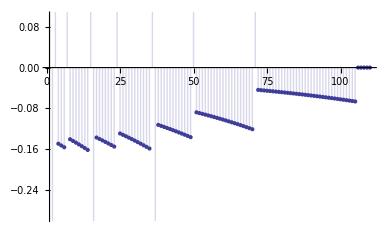

```mathematica
st[n_,a_]:=If[tk2[a,n,1.02]≠0,(-1)^(n+1)/n tk2[a,n,1.02] + 1/n,0]
DiscretePlot[st[n,8],{n,1,110}]
```

100000

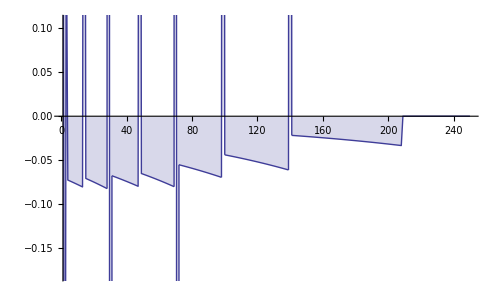

```mathematica
$RecursionLimit=100000
st[n_,a_]:=If[tk2[a,n,1.01]≠0,(-1)^(n+1)/n tk2[a,n,1.01] + 1/n,0]
DiscretePlot[st[n,8],{n,1,250}]
```

100000

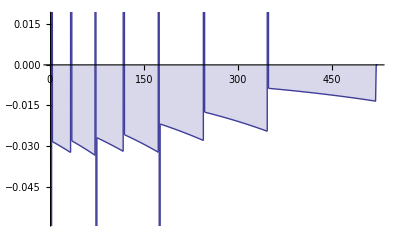

```mathematica
$RecursionLimit=100000
st[n_,a_]:=If[tk2[a,n,1.004]≠0,(-1)^(n+1)/n tk2[a,n,1.004] + 1/n,0]
DiscretePlot[st[n,8],{n,1,523}]
```

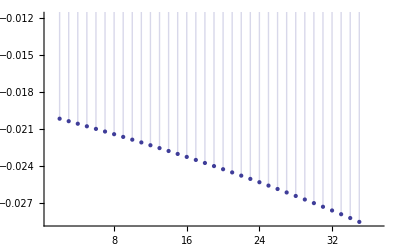

```mathematica
st[n_,a_]:=If[tk2[a,n,1.02]≠0,(-1)^(n+1)/n tk2[a,n,1.02] + 1/n,0]
DiscretePlot[st[n,2],{n,1,37}]
```

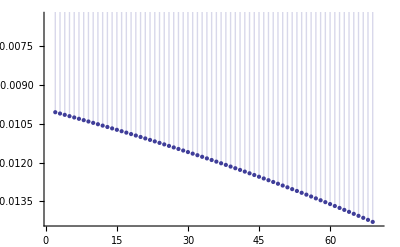

```mathematica
st[n_,a_]:=If[tk2[a,n,1.01]≠0,(-1)^(n+1)/n tk2[a,n,1.01] + 1/n,0]
DiscretePlot[st[n,2],{n,1,70}]
```

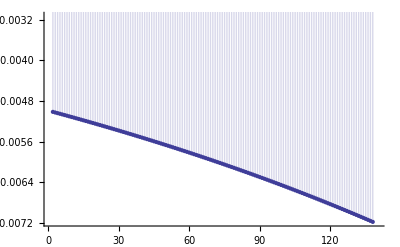

```mathematica
st[n_,a_]:=If[tk2[a,n,1.005]≠0,(-1)^(n+1)/n tk2[a,n,1.005] + 1/n,0]
DiscretePlot[st[n,2],{n,1,140}]
```

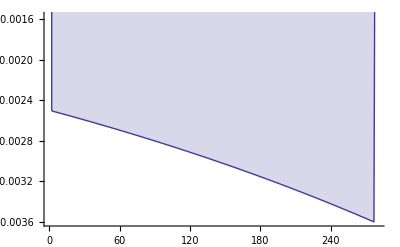

```mathematica
st[n_,a_]:=If[tk2[a,n,1.0025]≠0,(-1)^(n+1)/n tk2[a,n,1.0025] + 1/n,0]
DiscretePlot[st[n,2],{n,1,280}]
```

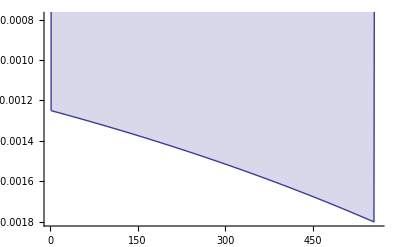

```mathematica
st[n_,a_]:=If[tk2[a,n,1.00125]≠0,(-1)^(n+1)/n tk2[a,n,1.00125] + 1/n,0]
DiscretePlot[st[n,2],{n,1,560}]
```